# Experiments Analysis :: Héctor Manuel Sánchez Castellanos

## Functions

## Libraries

```mathematica
SetDirectory[NotebookDirectory[]];
(*<<SoNA3BSAnalysis`*)
<<PajaroLocoPublic`
<<HypothesisTesting`
```

## Package Functions

### Descriptions

```mathematica
(*(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------------*)FixBitesListTail::usage="Converts NetLogo bites lists into Mathematica bites lists"
FixBitesListTails::usage="Converts NetLogo experiment bites lists into Mathematica bites lists"
GetExperimentSection::usage="Returns an XML section that is correctly tagged as such"
ConvertTicksToIntegersExperiment::usage="Converts the ticks values to integers in a single experiment"
ConvertTicksToIntegersExperimentsSet::usage="Converts ticks values into integers in an experiments set"
(*-------------------------------------------------------------------ExperimentHeader-------------------------------------------------------------------*)
GetExperimentsSetXMLData::usage="Returns the XML of all the experiments in XML format in the given path (relative to notebook's directory)"
GetExperimentsSetXMLDataAbsolute::usage="Returns the XML of all the experiments in XML format in the given absolute path"
GetExperimentHeader::usage="Returns the header section of an experiment in list form"
GetExperimentHeaderWithFixedDate::usage="Returns the header of an experiment with the date fixed to mathematica standard"
GetExperimentsSetHeader::usage="Returns the header of a set of experiments with the dates as a range (requires that the section is tagged: 'header')"
GetExperimentParameters::usage="Returns the parameters of a given experiment"
GetExperimentsSetParameters::usage="Returns the parameters that define the behavior of a set of experiments with the independent variables ordered (requires that the section is tagged: 'parameters')"
(*-------------------------------------------------------------------DirectContact----------------------------------------------------------------------*)
GetExperimentContactLabels::usage="Returns the names of the individuals involved in contacts situations of an experiment"
GetExperimentsSetContactLabels::usage="Returns the unrepeated names of the individuals involved in contacts situations of a set of experiments"
GetContactTally::usage="Returns the transition contacts counts"
GetExperimentContactsSection::usage="Returns the contacts section of a single experiment"
GetExperimentsSetContactsSection::usage="Returns the contacts section of a set of experiments"
GetExperimentContactsTransitionsWithPattern::usage="Returns the contacts matrix of an experiment given a labels pattern"
GetExperimentSetRawContactsTransitionsWithPattern::usage="Returns the individual contacts matrices of every experiment of a set"
GetExperimentSetContactsTransitionsWithPattern::usage="Returns the contacts matrix of a set of experiments given a labels pattern with the given mix function applied to the matrices"
FilterBetweenTicksExperiment::usage="Filters all the contacts that do not happen between the given ticks period"
FilterBetweenTicksExperimentSet::usage="Filters all the contacts that do not happen between the given ticks period in an experiments set"
GetExperimentSetContactsTransitionsWithPatternInIntervals::usage="Returns the contact matrices divided un fixed time intervals (cumulative)"
(*-------------------------------------------------------------------BitesContact-----------------------------------------------------------------------*)
GetExperimentBiteLabels::usage="Returns the names of the individuals involved in bites situations of an experiment"
GetExperimentsSetBiteLabels::usage="Returns the names of the individuals involved in bites situations of a set of experiments"
GetExperimentBitesSection::usage="Returns the bites section of a single experiment"
GetExperimentsSetBitesSection::usage="Returns the bites section of a set of experiments"
GetBitesLists::usage="Returns the bite lists of the experiments"
GetBitesTransitions::usage="Converts the bite lists into transitions lists"
GetBitesTransitionsCases::usage="Filters the bites in cases"
GetTransitionFrequencies::usage="Returns the transitions frequencies of a list of bites"
GetExperimentTransitionFrequencies::usage="Returns the transitions frequencies of an experiment"
GetExperimentTransitionFrequenciesFromTail::usage="Returns the transitions frequencies of an experiment from the tail section"
GetExperimentBitesTransitionsWithPattern::usage="Returns the bites transitions matrix from an experiment"
GetExperimentsSetRawBitesTransitionsWithPattern::usage="Returns the bites transitions of a set of experiments individualy"
GetExperimentsSetBitesTransitionsWithPattern::usage="Returns the bites transitions from a set of experiments"
(*-------------------------------------------------------------------HousesContact-------------------------------------------------------------------*)
GetExperimentHousesLabels::usage="Returns the names of the houses entities on an experiment"
GetExperimentsSetHousesLabels::usage="Returns the names of the houses entities on the experiments set"
GetHousesContactTally::usage="*Returns the tally of contacts with houses entities"
GetExperimentsSetHousesContactsSection::usage="Returns the houses contacts section of a set of experiments"
GetExperimentHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiment"
GetExperimentsSetHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiments set"
GetExperimentsSetRawHousesContactsTransitionsWithPattern::usage="Returns the individual experiments matrices of an experiments set"
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentTicksOutputs::usage="Returns the ticks outputs of an experiment"
GetExperimentsSetTicksOutputs::usage="Returns the ticks outputs of a set of experiments"
GetExperimentOutputTags::usage="Returns the names of the outputs of an experiment"
GetTaggedOutputFromExperimentsIndexes::usage="Returns the tick output of a given XML tag from the samples provided by the list of indexes (on the imported XML list of samples)"
GetExperimentSetIndexPositionsByIndependentVariableValues::usage="Returns the indexes that contain the combination of independent variables values"
GetExperimentSetTaggedOutputByIndependentVariableValues::usage="Returns the tagged output values of the samples that contain the combination of independent variables values (the return list of lists is ordered by ticks)"
GetExperimentSetIndexPositionsByIndependentVariableBins::usage="Returns the indexes (on the imported XML list of samples) from the samples that contain a certain combination of independent variables"
(*-------------------------------------------------------------------SCEIR Dynamics-----------------------------------------------------------------------*)
SCEIRInitializePersonsVectors::usage="Returns the initialized state vectors with the given indexes cases"
SCEIRInitializeCounterVectors::usage="Returns the initialized count vectors with zero values for each of them"
SCEIRInitializeVectors::usage="Initializes both vectors"
SCEIRUpdateCounters::usage="Updates the counters for each of the individuals in each state"
SCEIRTransitionState::usage="Returns the positions of the individuals that should make a transition given a state and threshold for counter"
SCEIRGenerateContagionMatrix::usage="Returns the bool values of the probabilities of an individual infecting the others without taking into account if the individual is himself in Infected state"
SCEIRGeneratePopulationContagionsMatrix::usage="Returns the matrix of the individuals being infected (columns) by others (rows)"
SCEIRUpdatePersonsVectorWithCondemnedIndividuals::usage="Returns the updated population vector with the replaced condemned individuals"
SCEIRSpreadDisease::usage="Spreads the disease between contacts probabilistically according to their contacts matrices"
SCEIRRunEpidemicEpoch::usage="Spread a disease through one epoch between the population in a network"
SCEIRNetworkEpidemicListEpochs::usage="Spreads a disease in a network returning the persons and counter vectors for each epoch"
SCEIRNetworkEpidemic::usage="Spread a disease in a network returning the persons and counter vectors for the last epoch"
SCEIRGenerateListPlotLists::usage="Returns the epidemic process lists so that they can be plotted"
SCEIRGraphEpidemicProcess::usage="Generates a graph of each step of the epidemic process"
SCEIRListPlotEpidemicProcess::usage="Generates a list plot of each step of the epidemic process"
SCEIRMatrixPlots::usage="Generates a Matrix Plot representation of each of the states in the epidemic process"
SCEIRGenerateMatrixPlotMatrices::usage="Generates a full condensed matrix for a matrix plot of the epidemic process"
(*-------------------------------------------------------------------SEIR Dynamics-----------------------------------------------------------------------*)
SEIRInitializePersonsVectors::usage=""
SEIRInitializeCounterVectors::usage=""
SEIRInitializeVectors::usage=""
SEIRUpdateCounters::usage=""
SEIRTransitionState::usage=""
SEIRGenerateContagionMatrix::usage=""
SEIRGeneratePopulationContagionsMatrix::usage=""
SEIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SEIRSpreadDisease::usage=""
SEIRRunEpidemicEpoch::usage=""
SEIRNetworkEpidemicListEpochs::usage=""
SEIRNetworkEpidemic::usage=""
SEIRGraphEpidemicProcess::usage=""
SEIRGenerateListPlotLists::usage=""
SEIRListPlotEpidemicProcess::usage=""
SEIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIR Dynamics-----------------------------------------------------------------------*)
SIRInitializePersonsVectors::usage=""
SIRInitializeCounterVectors::usage=""
SIRInitializeVectors::usage=""
SIRUpdateCounters::usage=""
SIRTransitionState::usage=""
SIRGenerateContagionMatrix::usage=""
SIRGeneratePopulationContagionsMatrix::usage=""
SIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SIRSpreadDisease::usage=""
SIRRunEpidemicEpoch::usage=""
SIRNetworkEpidemicListEpochs::usage=""
SIRNetworkEpidemic::usage=""
SIRGraphEpidemicProcess::usage=""
SIRGenerateListPlotLists::usage=""
SIRListPlotEpidemicProcess::usage=""
SIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIS Dynamics-----------------------------------------------------------------------*)
SISInitializePersonsVectors::usage=""
SISInitializeCounterVectors::usage=""
SISInitializeVectors::usage=""
SISUpdateCounters::usage=""
SISTransitionState::usage=""
SISGenerateContagionMatrix::usage=""
SISGeneratePopulationContagionsMatrix::usage=""
SISUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SISSpreadDisease::usage=""
SISRunEpidemicEpoch::usage=""
SISNetworkEpidemicListEpochs::usage=""
SISNetworkEpidemic::usage=""
SISGraphEpidemicProcess::usage=""
SISGenerateListPlotLists::usage=""
SISListPlotEpidemicProcess::usage=""
SISGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------Wrappers-----------------------------------------------------------------------*)
NetworkEpidemicListEpochs::usage="Simulates an epidemic returning the stages of the process"
GenerateListPlotLists::usage="Generates the list plots lists of the process"
ListPlotEpidemic::usage="Generates the final list plot of the process"
GenerateMatrixPlotMatrix::usage="Generates the final matrix of the process"
MatrixPlotEpidemic::usage="Generates the final matrix plot"
GraphEpidemicProcess::usage="Generates the graphs of each stage of the epidemic process"
ListPlotEpidemicProcess::usage="List plots an epidemic process in each stage"
MatrixPlotEpidemicProcess::usage="Generates the matrix plots at each stage of the process"
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------------------*)
GraphTransitionsFrequenciesSet::usage="Graphs a transitions frequencies set of matrices scaled to a global max of contacts"
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------------------*)
Summary::usage=""
NetworkEpidemicListEpochsRepeatOnIndexes::usage=""
NetworkEpidemicListEpochsRepeatSweep::usage=""
ListPlotRepeatOnIndexes::usage=""
MatrixPlotRepeatOnIndexes::usage=""*)
```

### Auxiliary

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------*)FixBitesListTail[experimentTail_]:=(StringReplace[#,{"["->" ","]"->" "," "->","}]//ToString//ToExpression)&/@experimentTail
FixBitesListTails[experimentsTails_]:=FixBitesListTail/@experimentsTails
GetExperimentSection[xmlExperimentData_,sectionTitle_]:=Cases[xmlExperimentData,XMLElement[sectionTitle,_,_],Infinity]
ConvertTicksToIntegersExperiment[cSectExperiment_]:=Module[{cSectOne=cSectExperiment,heads,tails,tailsFixed},heads=cSectOne[[All,1]];
tails=cSectOne[[All,2;;All]];
tailsFixed=Table[{#[[1]],#[[2]]//ToExpression}&/@tails[[i]],{i,1,tails//Length}];
(Prepend[#[[2]],#[[1]]]&/@({heads,tailsFixed}//Transpose))]
ConvertTicksToIntegersExperimentsSet[cSect_]:=ConvertTicksToIntegersExperiment/@cSect
```

### Head

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------ExperimentHeader------------------------------------------------------------*)
GetExperimentsSetXMLData[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",Directory[]<>path];
Import/@allFilesPaths]
GetExperimentsSetXMLDataAbsolute[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",path];
Import/@allFilesPaths]
GetExperimentHeader[xmlExperimentData_]:=Module[{temp},temp=GetExperimentSection[xmlExperimentData,"header"];
Cases[temp,XMLElement[a_,_,{c_}]->{a,c},{3}]]
GetExperimentHeaderWithFixedDate[xmlExperimentData_]:=Module[{header,datePosition},header=GetExperimentHeader[xmlExperimentData];
datePosition=(Position[header,{"date",_}]//Flatten)[[1]];
ReplacePart[header,{3,2}->DateList[header[[datePosition]][[2]]]]]
GetExperimentsSetHeader[xmlExperimentsDataSet_]:=Module[{headers,datePosition,sorted,dateRange},headers=(GetExperimentHeaderWithFixedDate[#]&/@xmlExperimentsDataSet);
datePosition=(Position[headers[[1]],{"date",_}]//Flatten)[[1]];
sorted=headers[[All,datePosition]][[All,2]]//Sort;
dateRange=DateString/@{sorted//First,sorted//Last};
ReplacePart[headers[[1]],datePosition->{"date",dateRange}]]
GetExperimentParameters[xmlExperimentData_]:=Module[{temp},temp=GetExperimentSection[xmlExperimentData,"parameters"];
Cases[temp,XMLElement[a_,{"id"->b_},{c_}]->{a,b,c},{3}]]
GetExperimentsSetParameters[xmlExperimentsDataSet_]:=Module[{experimentsData,independentPositions,independentTriplets,independentRanges,replacementRules},experimentsData=GetExperimentParameters[#]&/@xmlExperimentsDataSet;
independentPositions=Position[experimentsData[[1]],{"independent",_,_}]//Flatten;
independentTriplets=experimentsData[[All,#]]&/@independentPositions;
independentRanges=DeleteDuplicates/@(ToExpression/@(#[[All,3]]&/@independentTriplets));
replacementRules={#[[1]],3}->#[[2]]&/@({independentPositions,independentRanges}//Transpose);
ReplacePart[experimentsData[[1]],replacementRules]]
```

### Body

```mathematica
FilterBetweenTicksExperiment[fixedTicksCSect_,low_,high_]:=Module[{expCSect=fixedTicksCSect,section},Table[section=expCSect[[i]];
Cases[section[[2;;All]],{a_,b_}/;(b≥low&&b≤high)]//Prepend[#,section[[1]]]&,{i,1,expCSect//Length}]]
FilterBetweenTicksExperimentSet[cSect_,low_,high_]:=FilterBetweenTicksExperiment[#,low,high]&/@cSect
(*DirectContact*)
GetExperimentContactLabels[contactsSection_]:=Module[{b},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
b[[All,1]]]
GetExperimentsSetContactLabels[contactsSections_]:=(GetExperimentContactLabels/@contactsSections)//Flatten//DeleteDuplicates//Sort
GetContactTally[contactsSectionPart_]:=Module[{individual,contacts},individual=contactsSectionPart[[All,1]][[1]];
contacts=contactsSectionPart[[All,1]]//Drop[#,1]&//Tally;
{individual,contacts}]
GetExperimentContactsSection[experimentXMLData_]:=GetExperimentsSetContactsSection[{experimentXMLData}][[1]]
GetExperimentsSetContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails//ConvertTicksToIntegersExperimentsSet]
GetExperimentContactsTransitionsWithPattern[contactsSection_,pattern_]:=Module[{b,c},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
c=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@pattern,{i,1,pattern//Length}];
{c,pattern}]
GetExperimentSetRawContactsTransitionsWithPattern[contactsSections_,pattern_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]],contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPattern[contactsSections_,pattern_,mixFunction_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]]//mixFunction,contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPatternInIntervals[fixedTicksCSect_,labels_,mixFunction_,frames_]:=Module[{max,increment,low,high,fCSect,intervals},max=fixedTicksCSect[[1]][[All,2;;All]][[All,All,2]]//Flatten//Max;
increment=max/frames;
intervals=Table[low=0;high=i;
fCSect=FilterBetweenTicksExperimentSet[fixedTicksCSect,low,high];
GetExperimentSetContactsTransitionsWithPattern[fCSect,labels,mixFunction],{i,0,max,increment}]]
```

### Tail

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------BitesContact-------------------------------------------------------------------*)
GetExperimentBiteLabels[bites_]:=GetExperimentsSetBiteLabels[{bites}]
GetExperimentsSetBiteLabels[bites_]:=Module[{flat},flat=bites//Flatten//DeleteDuplicates;
Cases[flat,a_/;StringMatchQ[a,LetterCharacter..]]//Sort]
GetExperimentBitesSection[experimentXMLData_]:=GetExperimentsSetBitesSection[{experimentXMLData}][[1]]
GetExperimentsSetBitesSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"biteList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetBitesLists[fixedListsTails_]:=Map[#[[All,1]]&,Map[Drop[#,1]&,#]]&/@fixedListsTails
GetBitesTransitions[bitesLists_]:=((Partition[#,2,1]&/@#)//Flatten[#,1]&)&/@bitesLists
GetBitesTransitionsCases[bitesTransitions_]:=bitesTransitions//Flatten//DeleteDuplicates//Tuples[#,2]&
GetTransitionFrequencies[bitesTransitions_,agentsNames_]:=Module[{matrices},matrices=Table[Table[Count[j,{agentsNames[[i]],#}]&/@agentsNames,{i,1,agentsNames//Length}],{j,bitesTransitions}];
{matrices,ConstantArray[agentsNames,matrices//Length]}//Transpose]
GetExperimentTransitionFrequencies[transitionFrequencies_,mixFunction_]:={transitionFrequencies[[All,1]]//mixFunction,transitionFrequencies[[1,2]]}
GetExperimentTransitionFrequenciesFromTail[fixedListsTails_,pattern_,mixFunction_]:=Module[{bitesLists,bitesTransitions,agentsNames,transitionFrequencies},bitesLists=GetBitesLists[fixedListsTails];
bitesTransitions=GetBitesTransitions[bitesLists];
(*agentsNames=GetAgentsNames[bitesTransitions];*)transitionFrequencies=GetTransitionFrequencies[bitesTransitions,pattern];
GetExperimentTransitionFrequencies[transitionFrequencies,mixFunction]]
GetExperimentBitesTransitionsWithPattern[bitesExperimentList_,pattern_]:=GetExperimentTransitionFrequenciesFromTail[{bitesExperimentList},pattern,Total]
GetExperimentsSetRawBitesTransitionsWithPattern[bitesList_,pattern_]:={(GetExperimentTransitionFrequenciesFromTail[{#},pattern,Total]&/@bitesList)[[All,1]],pattern}
GetExperimentsSetBitesTransitionsWithPattern[bitesList_,pattern_,mixFunction_]:=GetExperimentTransitionFrequenciesFromTail[bitesList,pattern,mixFunction]
(*HouseContact*)
GetExperimentHousesLabels[contactsSection_]:=GetExperimentsSetHousesLabels[{contactsSection}]
GetExperimentsSetHousesLabels[contactsSection_]:=Module[{a,houses},Table[a=GetHousesContactTally[contactsSection[[i]]];
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort,{i,1,contactsSection//Length}]//Flatten//Sort//DeleteDuplicates]
GetHousesContactTally[contactsSectionPart_]:=Module[{housesNames,individualsNames,tallys},housesNames=Table[i[[All,1]],{i,contactsSectionPart[[All,2;;All]]}]//Flatten//DeleteDuplicates//Sort;
individualsNames=contactsSectionPart[[All,1]];
tallys=Tally/@contactsSectionPart[[All,2;;All,1]];
{individualsNames,tallys}//Transpose]
GetExperimentsSetHousesContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactHousesList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetExperimentHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{a,persons=patternPersons,houses=patternHouses,partial,matrix,transitions,b,c,labels},a=GetHousesContactTally[contactsSection];
b=a//Sort;
persons=b[[All,1]]//Flatten;
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort;
labels={persons,houses}//Flatten;
partial=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@labels,{i,1,b//Length}];
matrix={partial,ConstantArray[ConstantArray[0,partial[[1]]//Length],houses//Length]}//Flatten[#,1]&;
transitions={matrix,labels}]
GetExperimentsSetRawHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]],matrices[[1,2]]}]
GetExperimentsSetHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_,mixFunction_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]]//mixFunction,matrices[[1,2]]}]
```

### SIS

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIS-------------------------------------------------------------------*)
SISInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
{sPersonsVct*(1-iPersonsVct),iPersonsVct}]
SISInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct}]
SISInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SISUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SISTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex-1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex-1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SISGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SISGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SISSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SISGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SISGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SISRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SISUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SISTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SISSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SISNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SISInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SISRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SISNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SISGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SISGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SISListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SISListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SISGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected"},PlotStyle->{Blue,Green}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SISGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIR-------------------------------------------------------------------*)
SIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),iPersonsVct,rPersonsVct}]
SIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct,rCounterVct}]
SIRInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected","Recovered"},PlotStyle->{Blue,Green,Purple}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SEIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SEIR-------------------------------------------------------------------*)
SEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),ePersonsVct,iPersonsVct,rPersonsVct}]
SEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SEIRInitializeVectors[indexesCases_,populationSize_]:={SEIRInitializePersonsVectors[indexesCases,populationSize],SEIRInitializeCounterVectors[populationSize]}
SEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[3]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(E->I->R)*){personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
(*ContagionProcess*){personsVcts,counterVcts}=SEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
Total[{suceptible,exposed,infected,recovered}]]
```

### SCEIR

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SCEIR-------------------------------------------------------------------*)
SCEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
cPersonsVct=ConstantArray[0,populationSize];
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct}]
SCEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
cCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SCEIRInitializeVectors[indexesCases_,populationSize_]:={SCEIRInitializePersonsVectors[indexesCases,populationSize],SCEIRInitializeCounterVectors[populationSize]}
SCEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SCEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SCEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SCEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[4]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SCEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SCEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SCEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SCEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SCEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(C->E->I->R)*){personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[4]],4];
(*ContagionProcess*){personsVcts,counterVcts}=SCEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SCEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SCEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SCEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SCEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red],Style[#[[5]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SCEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SCEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SCEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SCEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SCEIRMatrixPlots[epidemicSCEIR_]:=Table[i//MatrixPlot,{i,(epidemicSCEIR[[1]]//Transpose)}]
SCEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,condemned,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
condemned=(#/.{1->-5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[5]]);
Total[{suceptible,condemned,exposed,infected,recovered}]]
```

### Graphs

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------*)
Options[GraphTransitionsFrequenciesSet]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic}}
GraphTransitionsFrequenciesSet[matricesSet_,OptionsPattern[]]:=GraphTransitionsFrequenciesWithMax[#,matricesSet[[All,1]]//Flatten//Max,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle],GraphLayout->OptionValue[GraphLayout],ImageSize->OptionValue[ImageSize],VertexSize->OptionValue[VertexSize],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@matricesSet
```

### Epidemic Wrappers

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------EpidemicWrappers---------------------------------------------------------*)
NetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SIR",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SEIR",SEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SCEIR",SCEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs]]]
GenerateListPlotLists[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGenerateListPlotLists[epidemicData[[1]]],"SIR",SIRGenerateListPlotLists[epidemicData[[1]]],"SEIR",SEIRGenerateListPlotLists[epidemicData[[1]]],"SCEIR",SCEIRGenerateListPlotLists[epidemicData[[1]]]]]
Options[ListPlotEpidemic]:={Joined->True,Thickness->.005}
ListPlotEpidemic[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{listPlotData},listPlotData=GenerateListPlotLists[epidemicData,epidemicType];
Switch[epidemicType,"SIS",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected"}],"SIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected","Recovered"}],"SEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}],"SCEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]]]
GenerateMatrixPlotMatrix[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SISGenerateMatrixPlotMatrices[epidemicData],"SIR",SIRGenerateMatrixPlotMatrices[epidemicData],"SEIR",SEIRGenerateMatrixPlotMatrices[epidemicData],"SCEIR",SCEIRGenerateMatrixPlotMatrices[epidemicData]]]
MatrixPlotEpidemic[epidemicData_,epidemicType_]:=Module[{},MatrixPlot[GenerateMatrixPlotMatrix[epidemicData,epidemicType],PlotTheme->"Scientific"]]
GraphEpidemicProcess[epidemicData_,contactsMatrix_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SIR",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SEIR",SEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SCEIR",SCEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic]]]
ListPlotEpidemicProcess[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{},Switch[epidemicType,"SIS",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SIR",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SEIR",SEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SCEIR",SCEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000]]]
MatrixPlotEpidemicProcess[epidemicData_,epidemicType_]:=Table[MatrixPlot[epidemicData[[1,i]]],{i,1,epidemicData[[1]]//Length}]
```

### Dynamics

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentOutputTags[experimentsXMLData_]:=Module[{output},output=GetExperimentSection[experimentsXMLData[[1]],"output"];
{"outputs",Cases[output,XMLElement[_,{"id"->a_},_]->a]//DeleteDuplicates}]
GetExperimentSetIndexPositionsByIndependentVariableBins[experimentsXMLData_]:=Module[{parametersList,indParPos,indParVal,tuples,patterns,constant,indParList,tuplesPositions},parametersList=GetExperimentParameters[#]&/@experimentsXMLData;
indParPos=GetExperimentsSetParameters[experimentsXMLData]//Position[#,{"independent",_,_}]&//Flatten;
indParVal=(GetExperimentsSetParameters[experimentsXMLData]//Cases[#,{"independent",_,a_}->a]&);
tuples=Tuples[indParVal];
patterns=Table[constant=ConstantArray[{_,_,"dummy"},parametersList[[1]][[indParPos]]//Length];
ReplacePart[constant[[j]],3->tuples[[i]][[j]]],{i,1,tuples//Length},{j,1,tuples[[1]]//Length}];
indParList=#[[indParPos]]&/@parametersList;
tuplesPositions=Position[ToExpression/@indParList,#]&/@patterns;
{tuplesPositions,tuples}//Transpose]
GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_]:=Module[{relationTable,index},relationTable=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSampleData];
index=Position[relationTable[[All,2]],independentVariablesValuesList]//Flatten;
(relationTable[[#,1]]&/@index)//Flatten]
GetTaggedOutputFromExperimentsIndexes[experimentsXMLData_,positionsList_,outputTag_]:=Module[{experimentsOutputsSections,output},experimentsOutputsSections=GetExperimentSection[#,"output"]&/@experimentsXMLData[[positionsList]];
output=Cases[#,XMLElement["output",{"id"->outputTag},{a_}]->a]&/@experimentsOutputsSections;
Map[ToExpression,output,Infinity]]
GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_,outputTag_]:=Module[{indexes},indexes=GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData,independentVariablesValuesList];
GetTaggedOutputFromExperimentsIndexes[xmlSampleData,indexes,outputTag]//Transpose]
GetExperimentTicksOutputs[xmlSampleData_]:=Module[{fixed,tickXML,test,test2,out},tickXML=GetExperimentSection[xmlSampleData,"tick"];
test=Cases[tickXML,XMLElement["tick",{"id"->a_},b__]->{a,b}];
test2=(test[[All,2]][[#]]//Cases[#,XMLElement[_,{"id"->c_},{d_}]->{c,d}]&)&/@Range[test//Length];
out={{ConstantArray["Tick",test//Length],test[[All,1]]}//Transpose,test2}//Transpose;
fixed=(Prepend[#[[2]],#[[1]]]&/@out)//Transpose;
Prepend[#[[All,2]]&/@fixed,fixed[[All,1,1]]]]
GetExperimentsSetTicksOutputs[xmlSet_]:=Module[{a},a=GetExperimentTicksOutputs[#]&/@xmlSet;
{a[[1,1]],{a[[All,2;;All]]}}]
```

### Sweeps

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------*)
Summary[epidemicData_,epidemicMatrix_,epidemicType_]:=Module[{listPlot,matrixPlot,graph},listPlot=ListPlotEpidemic[epidemicData,epidemicType,Joined->True];
matrixPlot=MatrixPlotEpidemic[epidemicData,epidemicType];
graph=GraphEpidemicProcess[epidemicData,epidemicMatrix[[1]],epidemicType]//Last;
Grid[{{"Development",Grid[{{listPlot,matrixPlot}}]},{"Graph",graph}},Frame->All,Background->{{LightBlue},None}]]
NetworkEpidemicListEpochsRepeatOnIndexes[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}}]
NetworkEpidemicListEpochsRepeatSweep[thresholds_,infectionProb_,contactsMatrixEpidemic_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},Table[sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,{j},epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}},{j,1,contactsMatrixEpidemic//Length}]//mixFunction]
ListPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=Show[Table[ListPlotEpidemic[epidemicData[[i]],epidemicType,Joined->True,Thickness->If[i==2,.0075,.001]],{i,1,3}]][[1,1,1]]
MatrixPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=MatrixPlotEpidemic[{(epidemicData[[All,1]]//Mean),(epidemicData[[All,2]]//Mean)},epidemicType]
```

## Old

```mathematica
PlotData[xmlSet_,point_,dependent_,sampleRate_]:=Module[{population,secondsPerTick,days,parameters,popDays,popDaysMean},
parameters=GetExperimentsSetParameters[xmlSet];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,dependent];

secondsPerTick=ToExpression[parameters[[2,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population//Length])//N];

popDays=({days,#}//Transpose)&/@(population//Transpose);
popDaysMean=({days,Mean/@population}//Transpose);
{popDays,popDaysMean}
]
GetExperimentsSetControlSection[experimentsXMLData_] := Module[{output, bitesListRaw, fixedListsTails},
output = GetExperimentSection[#, "output"] & /@ experimentsXMLData;
bitesListRaw = Map[Cases[#, XMLElement["output", {"id" -> "controlReleasesList"}, a_] -> a] &,output];
fixedListsTails = Map[ToString, FixBitesListTails[bitesListRaw], {5}][[All, 1]];
Table[{#[[1]]//ToExpression,#[[2]]//ToExpression,#[[3]]}&/@i,{i,fixedListsTails}]
]

PlotControlMeasures[xml_,point_,secondsPerTick_,sampleRate_]:=Module[{plot,ctl,lines},
plot=ListPlot[
PlotData[{xml},point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","PupaPopulation","LarvaPopulation","AdultPopulation"}
,Joined->True,(*PlotLegends->{"Total","Egg","Larva","Pupa","Adult"},*)LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All];
ctl=GetExperimentsSetControlSection[{xml}];
lines=Graphics[({LightRed,Thin,TechniqueLine[#[[1]],secondsPerTick]}//Flatten)&/@ctl[[1]]];
Show[plot,lines]
]

SwitchTechniqueColor[techniqueName_]:=Switch[techniqueName,
"BreedingReplacementSterila",{LightBlue},
"ReleaseSterile",{LightGreen},
"BreedingReplacementWolbachia",{LightRed},
"ReleaseWolbachia",{LightOrange},
"BreedingExtermination",{LightPurple},
"BreedingFumigation",{Gray}
]
TechniqueLine[tick_,secondsPerTick_]:=Line[{{TickToDay[tick,secondsPerTick]//N,0},{TickToDay[tick,secondsPerTick]//N,50000}}]
PlotAverage[averagePopulations_]:=ListPlot[
averagePopulations
,Joined->True,PlotLegends->{"Total","Egg","Larva","Pupa","Adult","Wolbachia","Sterile"},LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All
]
PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

AnalyseDataset[xmlSet_,sampleRate_]:=Module[{header,parameters,indexes,experimentDescriptionGrid,ctl,secondsPerTick,breedingExterminationRepetitions,breedingExterminationAveragePopulations,breedingExterminationAverage,point},
(*Control----------------------------*)
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
experimentDescriptionGrid=Grid[Flatten[{header,parameters},1],Background->LightBlue];(*out*)
(**)
ctl=GetExperimentsSetControlSection[xmlSet];
secondsPerTick=ToExpression[parameters[[2,3]]];
point=indexes[[1,2]];
breedingExterminationRepetitions=Show[PlotControlMeasures[#,point,secondsPerTick,sampleRate]&/@xmlSet];
breedingExterminationAveragePopulations=PlotData[xmlSet,point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","LarvaPopulation","PupaPopulation","AdultPopulation","WolbachiaPopulation","SterilePopulation"};
breedingExterminationAverage=PlotAverage[breedingExterminationAveragePopulations];
(*Output*)
{
{experimentDescriptionGrid,breedingExterminationRepetitions,breedingExterminationAverage},
{Flatten[{header,parameters},1],breedingExterminationRepetitions,breedingExterminationAveragePopulations}
}
]
SummaryAnalysis[path_,nCAnalysis_,sampleRate_]:=Module[{xmlSet,bEAnalysis,bEDiff,difference,bEGrid},
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bEAnalysis=AnalyseDataset[xmlSet,sampleRate];
bEDiff=PopulationsDynamicsDifference[{nCAnalysis[[2,3,5]]},{bEAnalysis[[2,3,5]]}];(*ADULTS, NOT TOTAL POPULATION*)
difference=ListPlot[bEDiff,Joined->True];
bEGrid=Grid[{{bEAnalysis[[1]],difference}//Flatten}]
]
Options[PlotRepetitions]:={PlotRange->{0,1500},ImageSize->600}
PlotRepetitions[repetitionsAndAveragesData_,stages_,colorsMean_,colorsRepetition_,OptionsPattern[]]:=Module[{colorsA=colorsMean,colors=colorsRepetition,iterationsPlot,averagesPlot,data,data2},
data=repetitionsAndAveragesData[[1]];
data2=repetitionsAndAveragesData[[2]];
iterationsPlot=Show[Table[ListPlot[data[[i]],Joined->True,PlotStyle->{colors[[i]]},ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]],{i,1,stages//Length}],ImageSize->Large];
averagesPlot=ListPlot[data2,Joined->True,PlotStyle->colorsA,ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]];
Grid[{
{
Show[{iterationsPlot,averagesPlot},ImageSize->OptionValue[ImageSize]],
Grid[Table[{colorsA[[i]],stages[[i]]},{i,1,stages//Length}]],
Grid[Table[{colors[[i]]},{i,1,stages//Length}]]
}
}]
]
FilterData[dataRaw_,{init_,end_}]:={
{dataRaw[[1,1]],dataRaw[[1,2]]},
{dataRaw[[2,1]][[All,init;;end]],dataRaw[[2,2]][[All,init;;end]]},
{dataRaw[[3,1]][[All,All,init;;end]],dataRaw[[3,2]][[All,init;;end]]}
};
TempPopPlot[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
DiffPercentage[test_,real_]:=Abs[(test-real)/real]
TempPopPlotShade[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
minAdults=Min/@(adults//Transpose);
maxAdults=Max/@(adults//Transpose);
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
dataMin={temps,minAdults}//Transpose;
dataMax={temps,maxAdults}//Transpose;
repetitionsPlot=ListPlot[{dataMin,dataMax},Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2,Filling->{2->{1}}];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
TempPopPlot2[dataRaw_,tempsIn_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
```

## Auxiliary

```mathematica
TickToDay[ticks_,secondsPerTick_]:=ticks*secondsPerTick*1/60*1/60*1/24
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
```

## Functions Schoolfield and Temperature

```mathematica
eggDevelopment={1.9858775,.24,10798,100000,14184};
larvaDevelopment={1.9858775,.2088,26018,55990,304.6};
pupaDevelopment={1.9858775,.384,14931,-472379,148};
gonotropicCycleA1Development={1.9858775,.216,15725,1756481,447.2};
gonotropicCycleA2Development={1.9858775,.372,15725,1756481,447.2};

SchoolfieldDevelopmentRatio[TK_,parametersList_]:=Module[{T,R,RdK,Ha,Hh,T12},
SchoolfieldDevelopmentRatioCore[TK,parametersList[[1]],parametersList[[2]],parametersList[[3]],parametersList[[4]],parametersList[[5]]]
]
SchoolfieldDevelopmentRatioCore[T_,R_,RdK_,Ha_,Hh_,T12_]:=RdK*((T+273.15)/298*ⅇ^(Ha/R*(1/298-1/(T+273.15))))/(1+ⅇ^(Hh/R*(1/T12-1/(T+273.15))))
CalculateSchoolfieldSet[Tc_,{eggDevelopment_,larvaDevelopment_,pupaDevelopment_,gonotropicCycleA1Development_,gonotropicCycleA2Development_}]:={
SchoolfieldDevelopmentRatio[Tc,eggDevelopment],
SchoolfieldDevelopmentRatio[Tc,larvaDevelopment],
SchoolfieldDevelopmentRatio[Tc,pupaDevelopment],
SchoolfieldDevelopmentRatio[Tc,gonotropicCycleA1Development],
SchoolfieldDevelopmentRatio[Tc,gonotropicCycleA2Development]
}
```

```mathematica
Grid[{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}//Transpose//Prepend[#,{"Egg","Larva","Pupa","GonotrophicA1","GonotrophicA2"}]&//Transpose//Prepend[#,{"","R","RdK","Ha","Hh","T12"}]&];
TeXForm[%];
```

## ODE Model*******

```mathematica
mlf[T_]:=.01+.9725*ⅇ^(-(T-278)/2.7035)
mpf[T_]:=.01+.9725*ⅇ^(-(T-278)/2.7035)
γ[l_,BS_,a0_]:=If[l/BS<a0,0,.63]
αf[α0_,BS_]:=α0/BS
CalculateStochasticModel[{elr_,lpr_,par_,ovr1_,ovr2_},{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{},
Clear[e,l,p,a1,a2];
NDSolve[{
e[0]==0,l[0]==initPop*.3,p[0]==initPop*.3,a1[0]==initPop*.2,a2[0]==initPop*.2,
e'[t]==egn*(ovr1*a1[t]+ovr2*a2[t])-me*e[t]-elr*(1-If[l[t]/BS<a0,0,.63])*e[t],
l'[t]==elr*(1-If[l[t]/BS<a0,0,.63])*e[t]-ml*l[t]-α*l[t]^2-lpr*l[t],
p'[t]==lpr*l[t]-mp*p[t]-par*p[t],
a1'[t]==par*ef*1/2*p[t]-ma*a1[t]-ovr1*a1[t],
a2'[t]==ovr1*a1[t]-ma*a2[t]
},{e,l,p,a1,a2},{t,0,time}]
]
(*CalculateStochasticModel2[temperature_,{eggDevelopment_,larvaDevelopment_,pupaDevelopment_,gonotropicCycleA1Development_,gonotropicCycleA2Development_},time_]:=Module[
{elr,lpr,par,ovr1,ovr2,soln},
{elr,lpr,par,ovr1,ovr2}=CalculateSchoolfieldSet[temperature,
{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}
];
]*)
CalculateAndRunStochasticModel[schoolfield_,{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{soln},
Clear[e,l,p,a1,a2];
soln=CalculateStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},initPop,time];
{
((e[#] /. soln[[1, 1]])&/@Range[1,time])/10,
(l[#] /. soln[[1, 2]])&/@Range[1,time],
(p[#] /. soln[[1, 3]])&/@Range[1,time],
(2*((a1[#]/.soln[[1,4]])+(a2[#]/.soln[[1,5]])))&/@Range[1,time]
}
]
```

```mathematica
CalculateAndRunStochasticModelFinal[temp_,{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{schoolfield,stochasticPopDynamics},
schoolfield=CalculateSchoolfieldSet[temp,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},initPop,time]
]
```

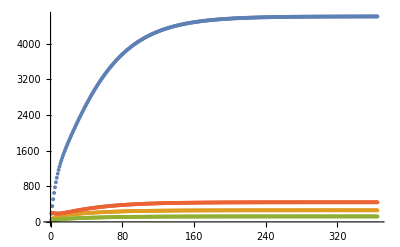

```mathematica
{bs,temperature}={25,25};
{BS,me,egn,ef,ma,α0}={bs,.01,63,.83,.09,1.5};
{a0,α,ml,mp}={.75, αf[α0, bs],mlf[temperature+273.15],mpf[temperature+273.15]};
schoolfield=CalculateSchoolfieldSet[temperature,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},250,365]//ListPlot
```

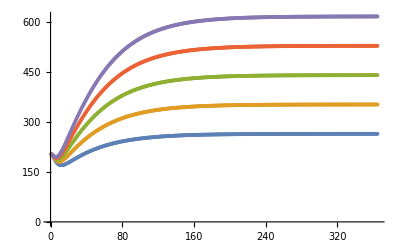

```mathematica
(*ERROR!!! HAS TO BE RUN TWICE TO WORK FOR WHATEVER REASON*)
Table[
{bs,temperature}={i,25};
{BS,me,egn,ef,ma,ml,mp,α0}={bs,.01,63,.83,.09,mlf[temperature+273.15],mpf[temperature+273.15],1.5};
{a0,α}={.75, αf[α0, bs]};
schoolfield=CalculateSchoolfieldSet[temperature,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},250,365][[4]]
,{i,15,35,5}]//ListPlot
```

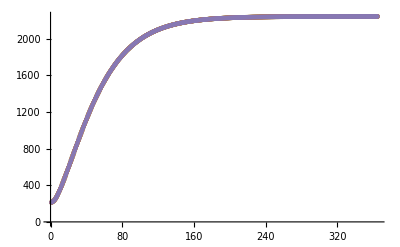

```mathematica
(*THESE TWO PLOTS SHOULD BE THE SAME*)
Table[CalculateAndRunStochasticModelFinal[30,{i,me,egn,ma,ml,mp,α,ef,a0},250,365],{i,15,35,5}][[All,4]]//ListPlot
```

## Comparison Functions

```mathematica
HeadComparisonBetweenABMAndMathematical[ABMPath_,sampleRate_]:=Module[{temperature,bs,abmData,meanABMValues,days,initPop,time,me,egn,ef,ma,ml,mp,α0,a0,α,schoolfield,soln,stochasticPopDynamics},
{temperature,bs}={ToExpression[StringTake[ABMPath,-2]],ToExpression[StringTake[ABMPath,{-4,-3}]]};
abmData=ReturnData[ParentDirectory[]<>ABMPath,{"EggsPopulation","LarvaPopulation","PupaPopulation","AdultPopulation"},sampleRate];
{meanABMValues,time,initPop }={(Transpose/@abmData[[2,1]])//Transpose,abmData[[2,1,1]]//Length,250};
(**)
{me,egn,ef,ma,ml,mp,α0}={.01,63,.83,.09,mlf[temperature+273.15],mpf[temperature+273.15],1.5};
{a0,α}={.75, αf[α0, bs]};
schoolfield=CalculateSchoolfieldSet[temperature,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{bs,me,egn,ma,ml,mp,α,ef,a0},initPop,time];
{stochasticPopDynamics,meanABMValues}
]
CompareABMAndMathematicalFactorialRatio[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]]},
Table[Mean/@(((#[[1]]-#[[2]])/(#[[2]]))&/@({meanABMValues[[i]],stochasticPopDynamics}//Transpose//N)),{i,1,meanABMValues//Length}]//Transpose]
CompareABMAndMathematicalFactorialDifference[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]]},Table[Mean/@((#[[1]]-#[[2]])&/@({meanABMValues[[i]],stochasticPopDynamics}//Transpose//N)),{i,1,meanABMValues//Length}]//Transpose]

CompareABMAndMathematicalFactorialDifferenceSS[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]],steadySim,steadyMath,out},
Clear[a,x];
steadySim=Table[(NonlinearModelFit[#[[Floor[.25*meanABMValues[[1]]//Length];;All]],a,{a},x]//Normal)&/@i,{i,meanABMValues}];
steadyMath=Last/@stochasticPopDynamics;
out=(#-steadyMath)&/@steadySim;
out//Transpose
]

CompareABMAndMathematicalFactorialRatioSS[headComparison_]:=Module[
{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]],steadySim,steadyMath,out},
Clear[a,x];
steadySim=Table[(NonlinearModelFit[#[[Floor[.25*meanABMValues[[1]]//Length];;All]],a,{a},x]//Normal)&/@i,{i,meanABMValues}];
steadyMath=Last/@stochasticPopDynamics;
out=(#-steadyMath)/steadyMath&/@steadySim;
out//Transpose
]
```

## Fit Density Dependend Model

```mathematica
FitNonLinearModel[dataRaw_,steps_]:=Module[{regressions,dataT,model,results,kValues,inputData,k,pfun,fit,functions,rValues},
(*Unsafe for a, k, r, t, x*)
(*Regression of k*)
Clear[a,x];
regressions=Table[
dataT=dataRaw[[2,2,i]][[Floor[(dataRaw[[2,2,1]]//Length)*.25];;All]];
model=NonlinearModelFit[dataT,a,{a},x]//Normal;
{model,Show[{ListPlot[dataT],Plot[model,{x,0,steps}]}]}
,{i,1,4}];
kValues=regressions[[All,1]];
(*Regression of r*)
Clear[τ,r,k];
τ=0;
results=Table[
inputData=dataRaw[[2,2,i]];
Clear[r,k];
k=kValues[[i]];
pfun=ParametricNDSolveValue[{
n'[t]==r*n[t]*((k-n[t-τ])/k),
n[0]==inputData[[1]]
},n,{t,0,2*steps},{r}];
fit=FindFit[inputData,pfun[r][t],{{r,1}},t]//Quiet;
{pfun,fit}
,{i,1,4}];
rValues=results[[All,2,1,2]];
(*Returning values*)
functions=(#[[1]][r][t]/.#[[2]])&/@results;
{kValues,rValues,functions}//Transpose
]
FitDensityDependentModel[meanABM_]:=Module[{k,pfun,fit,r,function},
Clear[a,x,k,r,t];
k=NonlinearModelFit[meanABM[[Floor[.25*(meanABM//Length)];;All]],a,{a},x]//Normal;
pfun=ParametricNDSolveValue[{
n'[t]==r*n[t]*((k-n[t])/k),
n[0]==meanABM[[1]]
},n,{t,0,2*(meanABM//Length)},{r}];
fit=(FindFit[meanABM,pfun[r][t],{{r,.05}},t]//Quiet);
r=fit[[1,2]];
function=(pfun[r][t]/.fit);
{function,{k,r}}
]
CompareABMAndMathematicalPlots[headTest_,lifeStage_]:=Module[{stochastic,meanABM,model},
stochastic=headTest[[1,lifeStage]];
meanABM=Mean/@(headTest[[2,All,lifeStage]]//Transpose)//N;
model=FitDensityDependentModel[meanABM];
Show[{
Plot[model[[1]],{t,0,meanABM//Length},PlotRange->{0,1.25*Max[{(stochastic//Last),(meanABM//Last)}]},PlotLegends->{"ABM Fit"},PlotLabel->{"r="<>ToString[model[[2,2]]],"k="<>ToString[model[[2,1]]]}],
ListPlot[{stochastic,meanABM},PlotStyle->{Red,Green},Joined->True,PlotLegends->{"Mathematical","ABM Data"}]
}]
]
```

## Other

```mathematica
GenerateTaguchiMatrix[comparisonsDifference_,paths_]:=Module[{bsTVct,means,sds,taguchiDifference,taguchiDifferenceFull},
bsTVct={StringTake[#,{-4,-3}],StringTake[#,-2]}&/@paths;
(*Difference*)
{means,sds}={{Prepend[Mean/@comparisonsDifference,"Mean"]}//Transpose,{Prepend[StandardDeviation/@comparisonsDifference,"SD"]}//Transpose};
taguchiDifference=Prepend[Flatten/@({bsTVct,comparisonsDifference}//Transpose),{"BreedingSites","Temperature",Range[comparisonsDifference//Transpose//Length]}//Flatten];
taguchiDifferenceFull=Append[Append[taguchiDifference//Transpose,means//Flatten],sds//Flatten]//Transpose
]
```

## Experiment 1 : Validation

## Copy Files (only needed the first time the experiment is run)

```mathematica
{sampleRate,secondsPerTick,lifeStage}={288,5*60,4};
rootPath="/GeneratedData/ValidationSweeps/";
files=FileNames["*.xml",ParentDirectory[]<>rootPath];
fileNames=Last[#]&/@(FileNameSplit[#]&/@files);
```

```mathematica
rawData=Import[#]&/@files;
headers=GetExperimentParameters[#]&/@rawData;
```

```mathematica
params=headers[[All,2;;3]];
paramsBS=Switch[#,"1",15,"2",20,"3",25,"4",30,"5",35]&/@params[[All,1,3]];
paramsT=ToExpression/@params[[All,2,3]];
paramsPairs=(ToString[#[[1]]]<>ToString[#[[2]]])&/@Transpose[{paramsBS,paramsT}];
```

```mathematica
directories=(CreateDirectory[ParentDirectory[]<>"/GeneratedData/ValidationSweeps/"<>#]&/@paramsPairs)//Quiet;
CopyFile[#[[1]],#[[3]]<>"/"<>#[[2]]]&/@({files,fileNames,directories}//Transpose)//Quiet;
```

## Load Data

```mathematica
{sampleRate,secondsPerTick,lifeStage,levelsT,levelsBS}={288,5*60,4,4,5};
paths="/GeneratedData/ValidationSweeps/PopDynAt"<>#&/@{
(*"1515",*)"1520","1525","1530","1535",
(*"2015",*)"2020","2025","2030","2035",
(*"2515",*)"2520","2525","2530","2535",
(*"3015",*)"3020","3025","3030","3035",
(*"3515",*)"3520","3525","3530","3535"
};
head=HeadComparisonBetweenABMAndMathematical[#,sampleRate]&/@paths;
body={comparisonsDifference,comparisonsRatio,comparisonsDifferenceSS,comparisonsRatioSS}={
(CompareABMAndMathematicalFactorialDifference[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialRatio[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialDifferenceSS[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialRatioSS[#]&/@head)[[All,lifeStage]]
};
```

## Taguchi

```mathematica
taguchis=GenerateTaguchiMatrix[#,paths]&/@body;
Export["DOE/Taguchi/"<>#[[2]],#[[1]]]&/@({taguchis,{"taguchiDifference.csv","taguchiRatio.csv","taguchiDifferenceSS.csv","taguchiRatioSS.csv"}}//Transpose);
TableForm[#]&/@taguchis
```

{BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | Mean | SD
15 | 20 | 1.59557 | 10.1246 | 8.83976 | 6.57232 | 3.27581 | 5.55488 | 3.24674 | 6.71767 | 5.74092 | 2.92724
15 | 25 | 10.1446 | 11.4702 | 20.0051 | 10.569 | 8.81904 | 15.4528 | 12.0981 | 6.17369 | 11.8416 | 4.23669
15 | 30 | -282.134 | -284.222 | -291.39 | -293.867 | -287.117 | -291.262 | -285.408 | -276.838 | -286.53 | 5.60661
15 | 35 | -578.718 | -583.555 | -577.218 | -579.939 | -571.381 | -566.073 | -568.579 | -560.381 | -573.231 | 7.91949
20 | 20 | 45.534 | 46.9991 | 54.97 | 50.6328 | 48.0921 | 46.0631 | 48.4642 | 44.9003 | 48.207 | 3.2915
20 | 25 | 111.149 | 119.085 | 120.039 | 107.76 | 119.12 | 114.957 | 116.678 | 119.248 | 116.004 | 4.45767
20 | 30 | -270.081 | -290.668 | -283.395 | -283.622 | -281.982 | -288.11 | -279.04 | -285.244 | -282.768 | 6.25272
20 | 35 | -712.759 | -708.834 | -709.514 | -700.445 | -697.544 | -707.398 | -705.416 | -694.055 | -704.496 | 6.49512
25 | 20 | 100.596 | 104.491 | 104.863 | 98.8691 | 100.695 | 103.985 | 100.131 | 97.3807 | 101.376 | 2.76573
25 | 25 | 226.763 | 247.042 | 257.315 | 229.803 | 244.809 | 242.263 | 232.321 | 241.862 | 240.272 | 10.1326
25 | 30 | -291.867 | -281.582 | -286.925 | -287.535 | -289.163 | -280.867 | -277.564 | -286.832 | -285.292 | 4.801
25 | 35 | -838.388 | -838.864 | -822.934 | -843.196 | -838.719 | -826.039 | -836.742 | -838.754 | -835.455 | 7.05868
30 | 20 | 156.658 | 155.855 | 156.082 | 155.454 | 151.635 | 160.396 | 153.21 | 161.646 | 156.367 | 3.33223
30 | 25 | 374.719 | 392.492 | 383.882 | 392.236 | 389.126 | 387.736 | 407.132 | 378.655 | 388.247 | 9.89714
30 | 30 | -255.095 | -277.391 | -270.629 | -255.804 | -248.019 | -282.943 | -257.304 | -264.664 | -263.981 | 12.126
30 | 35 | -930.171 | -963.857 | -969.002 | -955.339 | -974.136 | -971.078 | -933.758 | -954.543 | -956.485 | 16.6886
35 | 20 | 199.038 | 209.829 | 215.876 | 218.759 | 218.155 | 219.277 | 215.963 | 215.963 | 214.107 | 6.76265
35 | 25 | 528.123 | 530.971 | 534.681 | 539.506 | 535.268 | 537.902 | 528.768 | 543.338 | 534.82 | 5.35222
35 | 30 | -226.573 | -218.962 | -216.398 | -247.712 | -239.043 | -229.299 | -231.573 | -234.392 | -230.494 | 10.2428
35 | 35 | -1080.77 | -1077.18 | -1090.03 | -1080.13 | -1095.35 | -1076.54 | -1062.78 | -1071.71 | -1079.31 | 10.1307,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | Mean | SD
15 | 20 | 0.0652877 | 0.206803 | 0.207747 | 0.168272 | 0.0813084 | 0.144829 | 0.104065 | 0.152465 | 0.141347 | 0.0538963
15 | 25 | 0.0452589 | 0.0540254 | 0.0928918 | 0.0505725 | 0.0438454 | 0.0740172 | 0.0571364 | 0.0315196 | 0.0561584 | 0.0192074
15 | 30 | -0.32768 | -0.32938 | -0.340737 | -0.347576 | -0.333307 | -0.344049 | -0.330245 | -0.320702 | -0.33421 | 0.0091263
15 | 35 | -0.570821 | -0.577324 | -0.573309 | -0.578598 | -0.563355 | -0.562397 | -0.558103 | -0.553209 | -0.56714 | 0.00925159
20 | 20 | 0.766877 | 0.801992 | 0.95197 | 0.866568 | 0.812106 | 0.795725 | 0.809774 | 0.790636 | 0.824456 | 0.0587861
20 | 25 | 0.378993 | 0.404244 | 0.411385 | 0.365998 | 0.40446 | 0.390352 | 0.397558 | 0.406789 | 0.394972 | 0.01562
20 | 30 | -0.204055 | -0.234719 | -0.223259 | -0.227345 | -0.221084 | -0.228207 | -0.219921 | -0.221579 | -0.222521 | 0.00890944
20 | 35 | -0.526214 | -0.525363 | -0.52171 | -0.515947 | -0.51243 | -0.522048 | -0.518697 | -0.515018 | -0.519678 | 0.00498445
25 | 20 | 1.44944 | 1.49153 | 1.49172 | 1.41668 | 1.45527 | 1.49173 | 1.42864 | 1.39248 | 1.45219 | 0.0379293
25 | 25 | 0.640034 | 0.692508 | 0.727793 | 0.64468 | 0.697528 | 0.680351 | 0.650652 | 0.680818 | 0.676795 | 0.0301725
25 | 30 | -0.157065 | -0.1429 | -0.162107 | -0.150555 | -0.165739 | -0.146496 | -0.138013 | -0.161077 | -0.152994 | 0.0100133
25 | 35 | -0.486797 | -0.483461 | -0.472358 | -0.48932 | -0.4855 | -0.469646 | -0.48377 | -0.482992 | -0.48173 | 0.00697033
30 | 20 | 1.93494 | 1.93174 | 1.93323 | 1.93113 | 1.88837 | 1.98787 | 1.90359 | 1.99366 | 1.93807 | 0.0365511
30 | 25 | 0.895163 | 0.939719 | 0.930176 | 0.939062 | 0.937215 | 0.937354 | 0.98229 | 0.904184 | 0.933145 | 0.0262352
30 | 30 | -0.0665359 | -0.125611 | -0.102307 | -0.0792923 | -0.0801373 | -0.106527 | -0.0826328 | -0.0975712 | -0.0925767 | 0.0189499
30 | 35 | -0.432778 | -0.457129 | -0.453677 | -0.444107 | -0.455459 | -0.453308 | -0.436885 | -0.456089 | -0.448679 | 0.00949842
35 | 20 | 2.1854 | 2.29913 | 2.3629 | 2.376 | 2.3841 | 2.3932 | 2.36283 | 2.36283 | 2.3408 | 0.0688742
35 | 25 | 1.11177 | 1.10392 | 1.09973 | 1.1297 | 1.11236 | 1.12779 | 1.10623 | 1.1393 | 1.11635 | 0.0141708
35 | 30 | -0.0316796 | -0.0319436 | -0.0217958 | -0.0452853 | -0.0348604 | -0.0291796 | -0.0395431 | -0.046773 | -0.0351326 | 0.00839646
35 | 35 | -0.422675 | -0.435362 | -0.43167 | -0.431351 | -0.438571 | -0.414593 | -0.417037 | -0.425868 | -0.427141 | 0.0085987,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | Mean | SD
15 | 20 | 19.0002 | 27.6984 | 26.5209 | 24.4144 | 20.8463 | 22.9883 | 21.0534 | 24.1007 | 23.3278 | 2.95804
15 | 25 | -17.7095 | -16.7568 | -8.06449 | -17.5911 | -19.7805 | -12.4964 | -16.1651 | -22.1888 | -16.3441 | 4.35802
15 | 30 | -486.363 | -488.712 | -495.736 | -497.854 | -491.41 | -495.315 | -489.611 | -481.008 | -490.751 | 5.55762
15 | 35 | -816.718 | -821.303 | -815.049 | -817.505 | -809.297 | -803.428 | -806.185 | -798.09 | -810.947 | 7.99654
20 | 20 | 61.8037 | 63.496 | 71.4309 | 67.0404 | 64.3658 | 62.2652 | 64.7445 | 61.3422 | 64.5611 | 3.33345
20 | 25 | 61.545 | 69.7462 | 70.6456 | 58.1723 | 70.1368 | 65.5214 | 67.3261 | 69.7758 | 66.6087 | 4.5846
20 | 30 | -564.014 | -584.251 | -577.6 | -577.422 | -575.7 | -582.162 | -572.854 | -579.044 | -576.631 | 6.21467
20 | 35 | -1053.17 | -1048.89 | -1049.83 | -1040.53 | -1037.68 | -1047.73 | -1045.78 | -1033.76 | -1044.67 | 6.67822
25 | 20 | 116.09 | 119.712 | 120.12 | 114.22 | 116.22 | 119.433 | 115.357 | 112.54 | 116.712 | 2.77994
25 | 25 | 154.969 | 175.655 | 186.063 | 158.152 | 173.62 | 170.809 | 160.655 | 170.436 | 168.795 | 10.3232
25 | 30 | -678.01 | -667.543 | -672.697 | -673.632 | -674.809 | -666.969 | -663.501 | -672.744 | -671.238 | 4.78803
25 | 35 | -1283.78 | -1284.34 | -1268.07 | -1288.52 | -1284.13 | -1271.49 | -1281.95 | -1284.3 | -1280.82 | 7.11623
30 | 20 | 170.56 | 169.779 | 169.815 | 169.59 | 165.72 | 174.708 | 167.318 | 175.235 | 170.341 | 3.26717
30 | 25 | 280.566 | 298.738 | 289.957 | 298.584 | 295.265 | 293.661 | 313.353 | 284.756 | 294.36 | 10.0068
30 | 30 | -734.365 | -756.892 | -749.892 | -735.199 | -726.909 | -762.661 | -736.821 | -744.063 | -743.35 | 12.3038
30 | 35 | -1481.68 | -1516.22 | -1521.42 | -1507.71 | -1526.86 | -1523.66 | -1485.37 | -1506.5 | -1508.68 | 17.1214
35 | 20 | 211.343 | 222.059 | 228.402 | 230.804 | 230.585 | 231.591 | 228.467 | 228.467 | 226.465 | 6.78181
35 | 25 | 410.875 | 414.035 | 417.792 | 422.775 | 418.135 | 420.709 | 411.556 | 426.307 | 417.773 | 5.43547
35 | 30 | -800.741 | -793.007 | -790.267 | -821.889 | -813.451 | -803.427 | -805.735 | -808.48 | -804.625 | 10.3487
35 | 35 | -1741.27 | -1737.58 | -1750.58 | -1740.7 | -1756.1 | -1737. | -1722.97 | -1732.18 | -1739.8 | 10.2724,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | Mean | SD
15 | 20 | 0.489338 | 0.713356 | 0.68303 | 0.628778 | 0.536885 | 0.592051 | 0.542219 | 0.620701 | 0.600795 | 0.0761827
15 | 25 | -0.0675935 | -0.0639574 | -0.0307806 | -0.0671418 | -0.0754981 | -0.0476965 | -0.0616989 | -0.0846901 | -0.0623821 | 0.0166337
15 | 30 | -0.511317 | -0.513786 | -0.52117 | -0.523397 | -0.516623 | -0.520729 | -0.514732 | -0.505687 | -0.51593 | 0.00584276
15 | 35 | -0.695144 | -0.699048 | -0.693724 | -0.695814 | -0.688829 | -0.683833 | -0.68618 | -0.67929 | -0.690233 | 0.00680621
20 | 20 | 1.20691 | 1.23996 | 1.39491 | 1.30918 | 1.25695 | 1.21593 | 1.26434 | 1.1979 | 1.26076 | 0.0650961
20 | 25 | 0.176818 | 0.20038 | 0.202964 | 0.167128 | 0.201502 | 0.188242 | 0.193427 | 0.200465 | 0.191366 | 0.0131715
20 | 30 | -0.445318 | -0.461296 | -0.456045 | -0.455905 | -0.454546 | -0.459647 | -0.452298 | -0.457185 | -0.45528 | 0.00490681
20 | 35 | -0.672767 | -0.670034 | -0.670631 | -0.664693 | -0.662875 | -0.669293 | -0.668046 | -0.660369 | -0.667339 | 0.00426606
25 | 20 | 1.82815 | 1.88518 | 1.89161 | 1.79871 | 1.8302 | 1.8808 | 1.8166 | 1.77224 | 1.83794 | 0.0437776
25 | 25 | 0.357118 | 0.404789 | 0.428774 | 0.364454 | 0.400098 | 0.393621 | 0.370222 | 0.392762 | 0.38898 | 0.0237893
25 | 30 | -0.428683 | -0.422064 | -0.425323 | -0.425914 | -0.426659 | -0.421701 | -0.419509 | -0.425353 | -0.424401 | 0.0030273
25 | 35 | -0.656392 | -0.656683 | -0.648363 | -0.658819 | -0.656574 | -0.650109 | -0.655461 | -0.656662 | -0.654883 | 0.00363851
30 | 20 | 2.25223 | 2.24191 | 2.24238 | 2.23941 | 2.18831 | 2.307 | 2.20941 | 2.31396 | 2.24933 | 0.0431426
30 | 25 | 0.539899 | 0.574867 | 0.557969 | 0.574571 | 0.568183 | 0.565097 | 0.602991 | 0.547961 | 0.566442 | 0.0192563
30 | 30 | -0.387225 | -0.399103 | -0.395412 | -0.387665 | -0.383293 | -0.402145 | -0.388519 | -0.392338 | -0.391962 | 0.00648767
30 | 35 | -0.631564 | -0.646283 | -0.648503 | -0.642656 | -0.65082 | -0.649456 | -0.633135 | -0.642142 | -0.64307 | 0.00729794
35 | 20 | 2.40419 | 2.52609 | 2.59825 | 2.62558 | 2.62309 | 2.63453 | 2.59899 | 2.59899 | 2.57621 | 0.0771485
35 | 25 | 0.678833 | 0.684053 | 0.690261 | 0.698493 | 0.690828 | 0.695081 | 0.679957 | 0.704329 | 0.690229 | 0.00898029
35 | 30 | -0.362131 | -0.358634 | -0.357395 | -0.371695 | -0.367879 | -0.363346 | -0.36439 | -0.365631 | -0.363888 | 0.00468014
35 | 35 | -0.63638 | -0.635033 | -0.639782 | -0.636172 | -0.641799 | -0.634821 | -0.629693 | -0.633058 | -0.635842 | 0.00375425}

## Factorial

```mathematica
bsTVct={StringTake[#,{-4,-3}],StringTake[#,-2]}&/@paths;
factorials=Prepend[Flatten[Table[Table[Flatten[{bsTVct[[j]],#[[j,i]]}],{i,1,((#[[1]])//Length)}],{j,1,bsTVct//Length}],1],{"BreedingSites","Temperature","Value"}]&/@body;
Export["DOE/Factorial/"<>#[[2]],#[[1]]]&/@({factorials,{"factorialDifference.csv","factorialRatio.csv","factorialDifferenceSS.csv","factorialRatioSS.csv"}}//Transpose);
TableForm[#]&/@factorials
```

{BreedingSites | Temperature | Value
15 | 20 | 1.59557
15 | 20 | 10.1246
15 | 20 | 8.83976
15 | 20 | 6.57232
15 | 20 | 3.27581
15 | 20 | 5.55488
15 | 20 | 3.24674
15 | 20 | 6.71767
15 | 25 | 10.1446
15 | 25 | 11.4702
15 | 25 | 20.0051
15 | 25 | 10.569
15 | 25 | 8.81904
15 | 25 | 15.4528
15 | 25 | 12.0981
15 | 25 | 6.17369
15 | 30 | -282.134
15 | 30 | -284.222
15 | 30 | -291.39
15 | 30 | -293.867
15 | 30 | -287.117
15 | 30 | -291.262
15 | 30 | -285.408
15 | 30 | -276.838
15 | 35 | -578.718
15 | 35 | -583.555
15 | 35 | -577.218
15 | 35 | -579.939
15 | 35 | -571.381
15 | 35 | -566.073
15 | 35 | -568.579
15 | 35 | -560.381
20 | 20 | 45.534
20 | 20 | 46.9991
20 | 20 | 54.97
20 | 20 | 50.6328
20 | 20 | 48.0921
20 | 20 | 46.0631
20 | 20 | 48.4642
20 | 20 | 44.9003
20 | 25 | 111.149
20 | 25 | 119.085
20 | 25 | 120.039
20 | 25 | 107.76
20 | 25 | 119.12
20 | 25 | 114.957
20 | 25 | 116.678
20 | 25 | 119.248
20 | 30 | -270.081
20 | 30 | -290.668
20 | 30 | -283.395
20 | 30 | -283.622
20 | 30 | -281.982
20 | 30 | -288.11
20 | 30 | -279.04
20 | 30 | -285.244
20 | 35 | -712.759
20 | 35 | -708.834
20 | 35 | -709.514
20 | 35 | -700.445
20 | 35 | -697.544
20 | 35 | -707.398
20 | 35 | -705.416
20 | 35 | -694.055
25 | 20 | 100.596
25 | 20 | 104.491
25 | 20 | 104.863
25 | 20 | 98.8691
25 | 20 | 100.695
25 | 20 | 103.985
25 | 20 | 100.131
25 | 20 | 97.3807
25 | 25 | 226.763
25 | 25 | 247.042
25 | 25 | 257.315
25 | 25 | 229.803
25 | 25 | 244.809
25 | 25 | 242.263
25 | 25 | 232.321
25 | 25 | 241.862
25 | 30 | -291.867
25 | 30 | -281.582
25 | 30 | -286.925
25 | 30 | -287.535
25 | 30 | -289.163
25 | 30 | -280.867
25 | 30 | -277.564
25 | 30 | -286.832
25 | 35 | -838.388
25 | 35 | -838.864
25 | 35 | -822.934
25 | 35 | -843.196
25 | 35 | -838.719
25 | 35 | -826.039
25 | 35 | -836.742
25 | 35 | -838.754
30 | 20 | 156.658
30 | 20 | 155.855
30 | 20 | 156.082
30 | 20 | 155.454
30 | 20 | 151.635
30 | 20 | 160.396
30 | 20 | 153.21
30 | 20 | 161.646
30 | 25 | 374.719
30 | 25 | 392.492
30 | 25 | 383.882
30 | 25 | 392.236
30 | 25 | 389.126
30 | 25 | 387.736
30 | 25 | 407.132
30 | 25 | 378.655
30 | 30 | -255.095
30 | 30 | -277.391
30 | 30 | -270.629
30 | 30 | -255.804
30 | 30 | -248.019
30 | 30 | -282.943
30 | 30 | -257.304
30 | 30 | -264.664
30 | 35 | -930.171
30 | 35 | -963.857
30 | 35 | -969.002
30 | 35 | -955.339
30 | 35 | -974.136
30 | 35 | -971.078
30 | 35 | -933.758
30 | 35 | -954.543
35 | 20 | 199.038
35 | 20 | 209.829
35 | 20 | 215.876
35 | 20 | 218.759
35 | 20 | 218.155
35 | 20 | 219.277
35 | 20 | 215.963
35 | 20 | 215.963
35 | 25 | 528.123
35 | 25 | 530.971
35 | 25 | 534.681
35 | 25 | 539.506
35 | 25 | 535.268
35 | 25 | 537.902
35 | 25 | 528.768
35 | 25 | 543.338
35 | 30 | -226.573
35 | 30 | -218.962
35 | 30 | -216.398
35 | 30 | -247.712
35 | 30 | -239.043
35 | 30 | -229.299
35 | 30 | -231.573
35 | 30 | -234.392
35 | 35 | -1080.77
35 | 35 | -1077.18
35 | 35 | -1090.03
35 | 35 | -1080.13
35 | 35 | -1095.35
35 | 35 | -1076.54
35 | 35 | -1062.78
35 | 35 | -1071.71,BreedingSites | Temperature | Value
15 | 20 | 0.0652877
15 | 20 | 0.206803
15 | 20 | 0.207747
15 | 20 | 0.168272
15 | 20 | 0.0813084
15 | 20 | 0.144829
15 | 20 | 0.104065
15 | 20 | 0.152465
15 | 25 | 0.0452589
15 | 25 | 0.0540254
15 | 25 | 0.0928918
15 | 25 | 0.0505725
15 | 25 | 0.0438454
15 | 25 | 0.0740172
15 | 25 | 0.0571364
15 | 25 | 0.0315196
15 | 30 | -0.32768
15 | 30 | -0.32938
15 | 30 | -0.340737
15 | 30 | -0.347576
15 | 30 | -0.333307
15 | 30 | -0.344049
15 | 30 | -0.330245
15 | 30 | -0.320702
15 | 35 | -0.570821
15 | 35 | -0.577324
15 | 35 | -0.573309
15 | 35 | -0.578598
15 | 35 | -0.563355
15 | 35 | -0.562397
15 | 35 | -0.558103
15 | 35 | -0.553209
20 | 20 | 0.766877
20 | 20 | 0.801992
20 | 20 | 0.95197
20 | 20 | 0.866568
20 | 20 | 0.812106
20 | 20 | 0.795725
20 | 20 | 0.809774
20 | 20 | 0.790636
20 | 25 | 0.378993
20 | 25 | 0.404244
20 | 25 | 0.411385
20 | 25 | 0.365998
20 | 25 | 0.40446
20 | 25 | 0.390352
20 | 25 | 0.397558
20 | 25 | 0.406789
20 | 30 | -0.204055
20 | 30 | -0.234719
20 | 30 | -0.223259
20 | 30 | -0.227345
20 | 30 | -0.221084
20 | 30 | -0.228207
20 | 30 | -0.219921
20 | 30 | -0.221579
20 | 35 | -0.526214
20 | 35 | -0.525363
20 | 35 | -0.52171
20 | 35 | -0.515947
20 | 35 | -0.51243
20 | 35 | -0.522048
20 | 35 | -0.518697
20 | 35 | -0.515018
25 | 20 | 1.44944
25 | 20 | 1.49153
25 | 20 | 1.49172
25 | 20 | 1.41668
25 | 20 | 1.45527
25 | 20 | 1.49173
25 | 20 | 1.42864
25 | 20 | 1.39248
25 | 25 | 0.640034
25 | 25 | 0.692508
25 | 25 | 0.727793
25 | 25 | 0.64468
25 | 25 | 0.697528
25 | 25 | 0.680351
25 | 25 | 0.650652
25 | 25 | 0.680818
25 | 30 | -0.157065
25 | 30 | -0.1429
25 | 30 | -0.162107
25 | 30 | -0.150555
25 | 30 | -0.165739
25 | 30 | -0.146496
25 | 30 | -0.138013
25 | 30 | -0.161077
25 | 35 | -0.486797
25 | 35 | -0.483461
25 | 35 | -0.472358
25 | 35 | -0.48932
25 | 35 | -0.4855
25 | 35 | -0.469646
25 | 35 | -0.48377
25 | 35 | -0.482992
30 | 20 | 1.93494
30 | 20 | 1.93174
30 | 20 | 1.93323
30 | 20 | 1.93113
30 | 20 | 1.88837
30 | 20 | 1.98787
30 | 20 | 1.90359
30 | 20 | 1.99366
30 | 25 | 0.895163
30 | 25 | 0.939719
30 | 25 | 0.930176
30 | 25 | 0.939062
30 | 25 | 0.937215
30 | 25 | 0.937354
30 | 25 | 0.98229
30 | 25 | 0.904184
30 | 30 | -0.0665359
30 | 30 | -0.125611
30 | 30 | -0.102307
30 | 30 | -0.0792923
30 | 30 | -0.0801373
30 | 30 | -0.106527
30 | 30 | -0.0826328
30 | 30 | -0.0975712
30 | 35 | -0.432778
30 | 35 | -0.457129
30 | 35 | -0.453677
30 | 35 | -0.444107
30 | 35 | -0.455459
30 | 35 | -0.453308
30 | 35 | -0.436885
30 | 35 | -0.456089
35 | 20 | 2.1854
35 | 20 | 2.29913
35 | 20 | 2.3629
35 | 20 | 2.376
35 | 20 | 2.3841
35 | 20 | 2.3932
35 | 20 | 2.36283
35 | 20 | 2.36283
35 | 25 | 1.11177
35 | 25 | 1.10392
35 | 25 | 1.09973
35 | 25 | 1.1297
35 | 25 | 1.11236
35 | 25 | 1.12779
35 | 25 | 1.10623
35 | 25 | 1.1393
35 | 30 | -0.0316796
35 | 30 | -0.0319436
35 | 30 | -0.0217958
35 | 30 | -0.0452853
35 | 30 | -0.0348604
35 | 30 | -0.0291796
35 | 30 | -0.0395431
35 | 30 | -0.046773
35 | 35 | -0.422675
35 | 35 | -0.435362
35 | 35 | -0.43167
35 | 35 | -0.431351
35 | 35 | -0.438571
35 | 35 | -0.414593
35 | 35 | -0.417037
35 | 35 | -0.425868,BreedingSites | Temperature | Value
15 | 20 | 19.0002
15 | 20 | 27.6984
15 | 20 | 26.5209
15 | 20 | 24.4144
15 | 20 | 20.8463
15 | 20 | 22.9883
15 | 20 | 21.0534
15 | 20 | 24.1007
15 | 25 | -17.7095
15 | 25 | -16.7568
15 | 25 | -8.06449
15 | 25 | -17.5911
15 | 25 | -19.7805
15 | 25 | -12.4964
15 | 25 | -16.1651
15 | 25 | -22.1888
15 | 30 | -486.363
15 | 30 | -488.712
15 | 30 | -495.736
15 | 30 | -497.854
15 | 30 | -491.41
15 | 30 | -495.315
15 | 30 | -489.611
15 | 30 | -481.008
15 | 35 | -816.718
15 | 35 | -821.303
15 | 35 | -815.049
15 | 35 | -817.505
15 | 35 | -809.297
15 | 35 | -803.428
15 | 35 | -806.185
15 | 35 | -798.09
20 | 20 | 61.8037
20 | 20 | 63.496
20 | 20 | 71.4309
20 | 20 | 67.0404
20 | 20 | 64.3658
20 | 20 | 62.2652
20 | 20 | 64.7445
20 | 20 | 61.3422
20 | 25 | 61.545
20 | 25 | 69.7462
20 | 25 | 70.6456
20 | 25 | 58.1723
20 | 25 | 70.1368
20 | 25 | 65.5214
20 | 25 | 67.3261
20 | 25 | 69.7758
20 | 30 | -564.014
20 | 30 | -584.251
20 | 30 | -577.6
20 | 30 | -577.422
20 | 30 | -575.7
20 | 30 | -582.162
20 | 30 | -572.854
20 | 30 | -579.044
20 | 35 | -1053.17
20 | 35 | -1048.89
20 | 35 | -1049.83
20 | 35 | -1040.53
20 | 35 | -1037.68
20 | 35 | -1047.73
20 | 35 | -1045.78
20 | 35 | -1033.76
25 | 20 | 116.09
25 | 20 | 119.712
25 | 20 | 120.12
25 | 20 | 114.22
25 | 20 | 116.22
25 | 20 | 119.433
25 | 20 | 115.357
25 | 20 | 112.54
25 | 25 | 154.969
25 | 25 | 175.655
25 | 25 | 186.063
25 | 25 | 158.152
25 | 25 | 173.62
25 | 25 | 170.809
25 | 25 | 160.655
25 | 25 | 170.436
25 | 30 | -678.01
25 | 30 | -667.543
25 | 30 | -672.697
25 | 30 | -673.632
25 | 30 | -674.809
25 | 30 | -666.969
25 | 30 | -663.501
25 | 30 | -672.744
25 | 35 | -1283.78
25 | 35 | -1284.34
25 | 35 | -1268.07
25 | 35 | -1288.52
25 | 35 | -1284.13
25 | 35 | -1271.49
25 | 35 | -1281.95
25 | 35 | -1284.3
30 | 20 | 170.56
30 | 20 | 169.779
30 | 20 | 169.815
30 | 20 | 169.59
30 | 20 | 165.72
30 | 20 | 174.708
30 | 20 | 167.318
30 | 20 | 175.235
30 | 25 | 280.566
30 | 25 | 298.738
30 | 25 | 289.957
30 | 25 | 298.584
30 | 25 | 295.265
30 | 25 | 293.661
30 | 25 | 313.353
30 | 25 | 284.756
30 | 30 | -734.365
30 | 30 | -756.892
30 | 30 | -749.892
30 | 30 | -735.199
30 | 30 | -726.909
30 | 30 | -762.661
30 | 30 | -736.821
30 | 30 | -744.063
30 | 35 | -1481.68
30 | 35 | -1516.22
30 | 35 | -1521.42
30 | 35 | -1507.71
30 | 35 | -1526.86
30 | 35 | -1523.66
30 | 35 | -1485.37
30 | 35 | -1506.5
35 | 20 | 211.343
35 | 20 | 222.059
35 | 20 | 228.402
35 | 20 | 230.804
35 | 20 | 230.585
35 | 20 | 231.591
35 | 20 | 228.467
35 | 20 | 228.467
35 | 25 | 410.875
35 | 25 | 414.035
35 | 25 | 417.792
35 | 25 | 422.775
35 | 25 | 418.135
35 | 25 | 420.709
35 | 25 | 411.556
35 | 25 | 426.307
35 | 30 | -800.741
35 | 30 | -793.007
35 | 30 | -790.267
35 | 30 | -821.889
35 | 30 | -813.451
35 | 30 | -803.427
35 | 30 | -805.735
35 | 30 | -808.48
35 | 35 | -1741.27
35 | 35 | -1737.58
35 | 35 | -1750.58
35 | 35 | -1740.7
35 | 35 | -1756.1
35 | 35 | -1737.
35 | 35 | -1722.97
35 | 35 | -1732.18,BreedingSites | Temperature | Value
15 | 20 | 0.489338
15 | 20 | 0.713356
15 | 20 | 0.68303
15 | 20 | 0.628778
15 | 20 | 0.536885
15 | 20 | 0.592051
15 | 20 | 0.542219
15 | 20 | 0.620701
15 | 25 | -0.0675935
15 | 25 | -0.0639574
15 | 25 | -0.0307806
15 | 25 | -0.0671418
15 | 25 | -0.0754981
15 | 25 | -0.0476965
15 | 25 | -0.0616989
15 | 25 | -0.0846901
15 | 30 | -0.511317
15 | 30 | -0.513786
15 | 30 | -0.52117
15 | 30 | -0.523397
15 | 30 | -0.516623
15 | 30 | -0.520729
15 | 30 | -0.514732
15 | 30 | -0.505687
15 | 35 | -0.695144
15 | 35 | -0.699048
15 | 35 | -0.693724
15 | 35 | -0.695814
15 | 35 | -0.688829
15 | 35 | -0.683833
15 | 35 | -0.68618
15 | 35 | -0.67929
20 | 20 | 1.20691
20 | 20 | 1.23996
20 | 20 | 1.39491
20 | 20 | 1.30918
20 | 20 | 1.25695
20 | 20 | 1.21593
20 | 20 | 1.26434
20 | 20 | 1.1979
20 | 25 | 0.176818
20 | 25 | 0.20038
20 | 25 | 0.202964
20 | 25 | 0.167128
20 | 25 | 0.201502
20 | 25 | 0.188242
20 | 25 | 0.193427
20 | 25 | 0.200465
20 | 30 | -0.445318
20 | 30 | -0.461296
20 | 30 | -0.456045
20 | 30 | -0.455905
20 | 30 | -0.454546
20 | 30 | -0.459647
20 | 30 | -0.452298
20 | 30 | -0.457185
20 | 35 | -0.672767
20 | 35 | -0.670034
20 | 35 | -0.670631
20 | 35 | -0.664693
20 | 35 | -0.662875
20 | 35 | -0.669293
20 | 35 | -0.668046
20 | 35 | -0.660369
25 | 20 | 1.82815
25 | 20 | 1.88518
25 | 20 | 1.89161
25 | 20 | 1.79871
25 | 20 | 1.8302
25 | 20 | 1.8808
25 | 20 | 1.8166
25 | 20 | 1.77224
25 | 25 | 0.357118
25 | 25 | 0.404789
25 | 25 | 0.428774
25 | 25 | 0.364454
25 | 25 | 0.400098
25 | 25 | 0.393621
25 | 25 | 0.370222
25 | 25 | 0.392762
25 | 30 | -0.428683
25 | 30 | -0.422064
25 | 30 | -0.425323
25 | 30 | -0.425914
25 | 30 | -0.426659
25 | 30 | -0.421701
25 | 30 | -0.419509
25 | 30 | -0.425353
25 | 35 | -0.656392
25 | 35 | -0.656683
25 | 35 | -0.648363
25 | 35 | -0.658819
25 | 35 | -0.656574
25 | 35 | -0.650109
25 | 35 | -0.655461
25 | 35 | -0.656662
30 | 20 | 2.25223
30 | 20 | 2.24191
30 | 20 | 2.24238
30 | 20 | 2.23941
30 | 20 | 2.18831
30 | 20 | 2.307
30 | 20 | 2.20941
30 | 20 | 2.31396
30 | 25 | 0.539899
30 | 25 | 0.574867
30 | 25 | 0.557969
30 | 25 | 0.574571
30 | 25 | 0.568183
30 | 25 | 0.565097
30 | 25 | 0.602991
30 | 25 | 0.547961
30 | 30 | -0.387225
30 | 30 | -0.399103
30 | 30 | -0.395412
30 | 30 | -0.387665
30 | 30 | -0.383293
30 | 30 | -0.402145
30 | 30 | -0.388519
30 | 30 | -0.392338
30 | 35 | -0.631564
30 | 35 | -0.646283
30 | 35 | -0.648503
30 | 35 | -0.642656
30 | 35 | -0.65082
30 | 35 | -0.649456
30 | 35 | -0.633135
30 | 35 | -0.642142
35 | 20 | 2.40419
35 | 20 | 2.52609
35 | 20 | 2.59825
35 | 20 | 2.62558
35 | 20 | 2.62309
35 | 20 | 2.63453
35 | 20 | 2.59899
35 | 20 | 2.59899
35 | 25 | 0.678833
35 | 25 | 0.684053
35 | 25 | 0.690261
35 | 25 | 0.698493
35 | 25 | 0.690828
35 | 25 | 0.695081
35 | 25 | 0.679957
35 | 25 | 0.704329
35 | 30 | -0.362131
35 | 30 | -0.358634
35 | 30 | -0.357395
35 | 30 | -0.371695
35 | 30 | -0.367879
35 | 30 | -0.363346
35 | 30 | -0.36439
35 | 30 | -0.365631
35 | 35 | -0.63638
35 | 35 | -0.635033
35 | 35 | -0.639782
35 | 35 | -0.636172
35 | 35 | -0.641799
35 | 35 | -0.634821
35 | 35 | -0.629693
35 | 35 | -0.633058}

## Comparison Plots

### Experiments plots

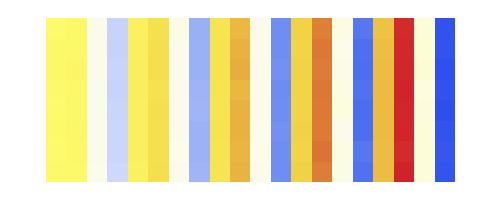
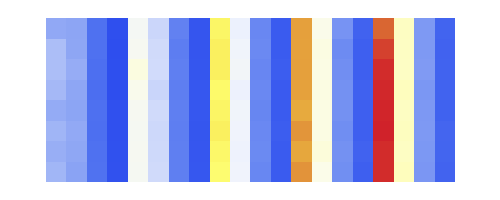
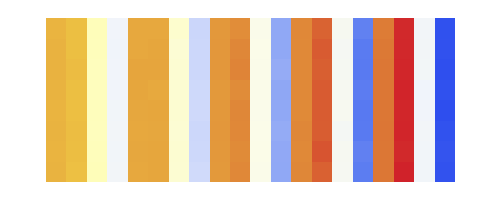
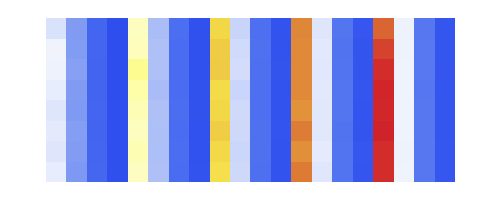

{Plots/Repetitions/experimentsDifferences.png,Plots/Repetitions/experimentsRatios.png,Plots/Repetitions/experimentsDifferencesSS.png,Plots/Repetitions/experimentsRatiosSS.png}

```mathematica
matrices=ArrayPlot[#[[All,1;;All]]//Transpose,
ColorFunction->"TemperatureMap",
PlotLegends->Placed[Automatic,Below],
ImageSize->500,
FrameTicks->{
{Range[body[[1,1]]//Length],None},
{{Range[#//Length],(Table[Table[Rotate["B"<>ToString[j]"T"<>ToString[i],90Degree],{i,20,35,5}],{j,15,35,5}]//Flatten)}//Transpose,
{Range[#//Length],((Rotate["μ ["<>ToString[#[[1]]]<>"] σ ["<>ToString[#[[2]]]<>"]",90Degree])&/@({Flatten[Partition[Mean/@#,5]],Flatten[Partition[StandardDeviation/@#,5]]}//Transpose))}//Transpose
}
}
]&/@body
Export["Plots/Repetitions/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"experimentsDifferences.png","experimentsRatios.png","experimentsDifferencesSS.png","experimentsRatiosSS.png"},matrices}//Transpose)
```

### Contours

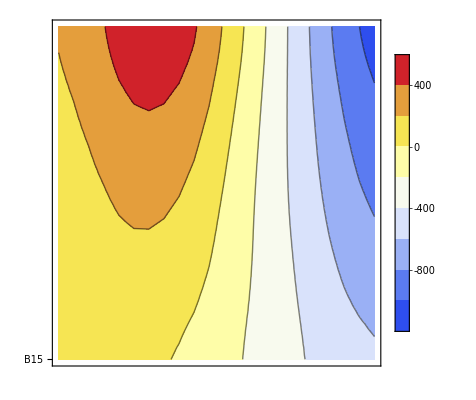
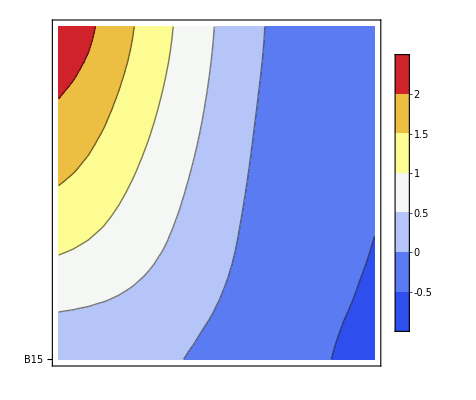
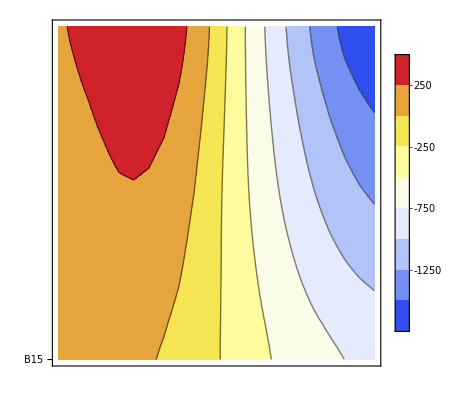
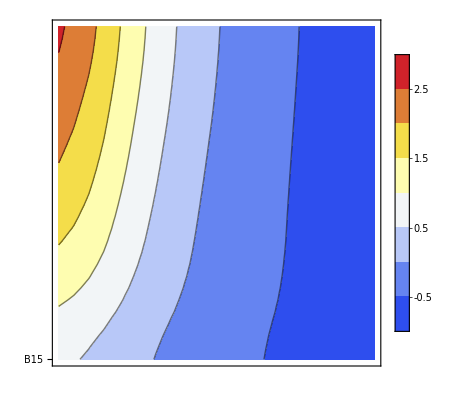

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

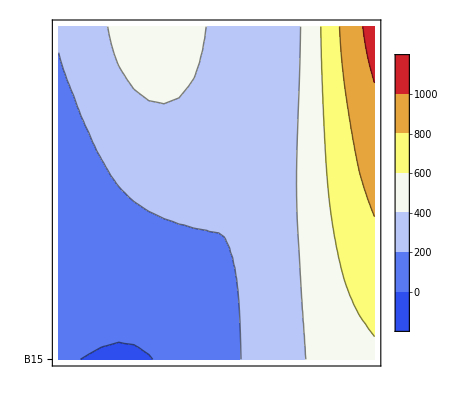
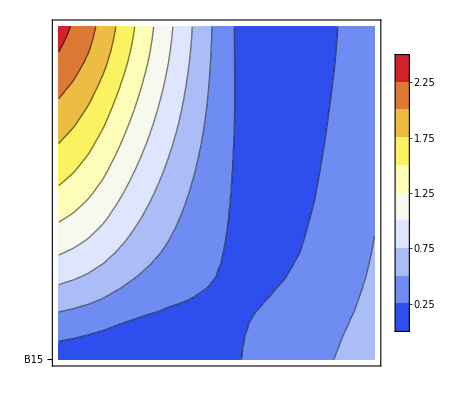
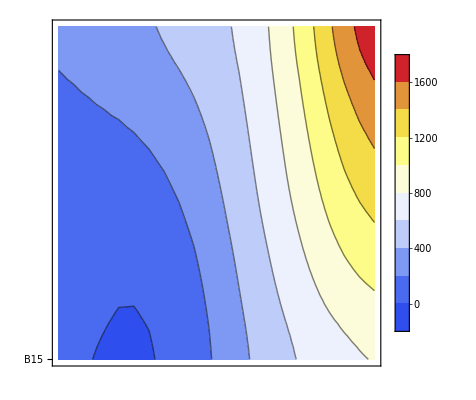
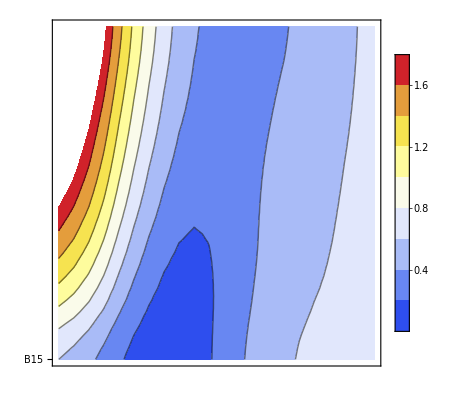

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{Plots/Real/contourDifferences.png,Plots/Real/contourRatios.png,Plots/Real/contourDifferencesSS.png,Plots/Real/contourRatiosSS.png}

{Plots/Real/contourDifferencesAbs.png,Plots/Real/contourRatiosAbs.png,Plots/Real/contourDifferencesSSAbs.png,Plots/Real/contourRatiosSSAbs.png}

{Plots/Real/3dcontourDifferences.png,Plots/Real/3dcontourRatios.png,Plots/Real/3dcontourDifferencesSS.png,Plots/Real/3dcontourRatiosSS.png}

{Plots/Real/3dcontourDifferencesAbs.png,Plots/Real/3dcontourRatiosAbs.png,Plots/Real/3dcontourDifferencesSSAbs.png,Plots/Real/3dcontourRatiosSSAbs.png}

```mathematica
partitions=Partition[Mean/@#,levelsT]&/@body;
contoursA=ListContourPlot[#,
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
InterpolationOrder->2,
FrameTicks->{
{{Range[100],("B"<>ToString[#])&/@Range[15,510,5]}//Transpose,None},
{None,{Range[99],("T"<>ToString[#])&/@Range[20,510,5]}//Transpose}
}
]&/@partitions
threeDA=ListPlot3D[#,ColorFunction->"TemperatureMap",InterpolationOrder->2]&/@partitions
contoursB=ListContourPlot[#//Abs,
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
InterpolationOrder->2,
FrameTicks->{
{{Range[100],("B"<>ToString[#])&/@Range[15,510,5]}//Transpose,None},
{None,{Range[99],("T"<>ToString[#])&/@Range[20,510,5]}//Transpose}
}
]&/@partitions
threeDB=ListPlot3D[#//Abs,ColorFunction->"TemperatureMap",InterpolationOrder->2]&/@partitions

Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"contourDifferences.png","contourRatios.png","contourDifferencesSS.png","contourRatiosSS.png"},contoursA}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"contourDifferencesAbs.png","contourRatiosAbs.png","contourDifferencesSSAbs.png","contourRatiosSSAbs.png"},contoursB}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"3dcontourDifferences.png","3dcontourRatios.png","3dcontourDifferencesSS.png","3dcontourRatiosSS.png"},threeDA}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"3dcontourDifferencesAbs.png","3dcontourRatiosAbs.png","3dcontourDifferencesSSAbs.png","3dcontourRatiosSSAbs.png"},threeDB}//Transpose)
```

## Minitab Fits

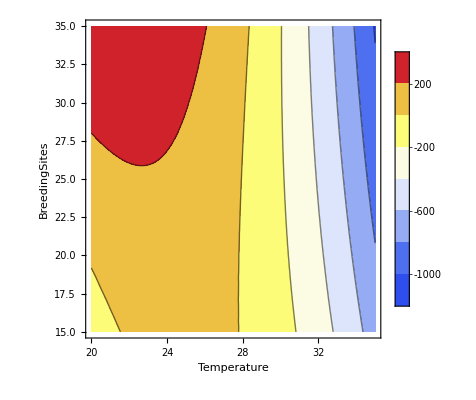
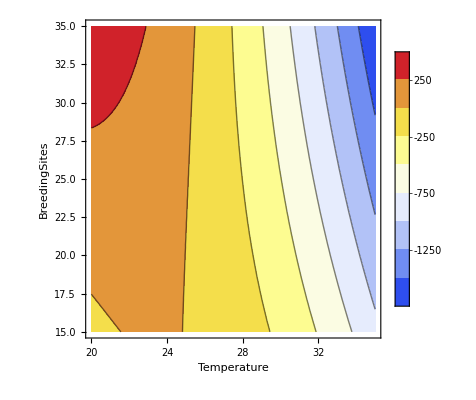
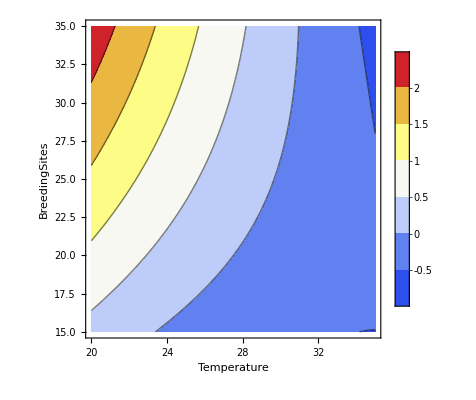
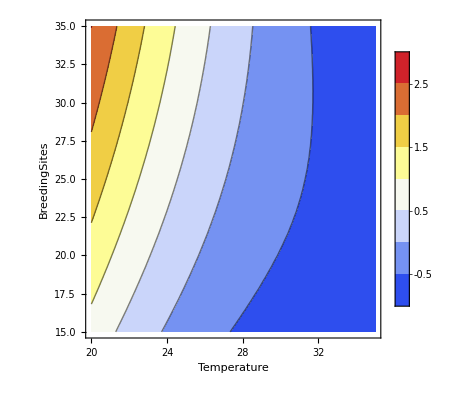

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

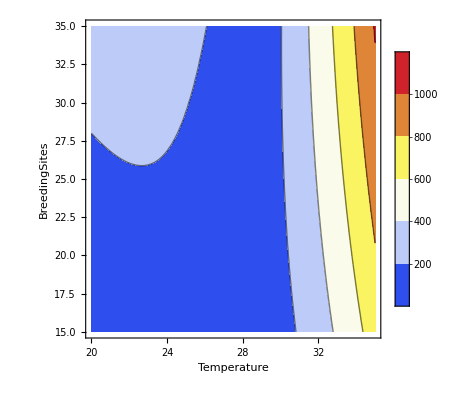
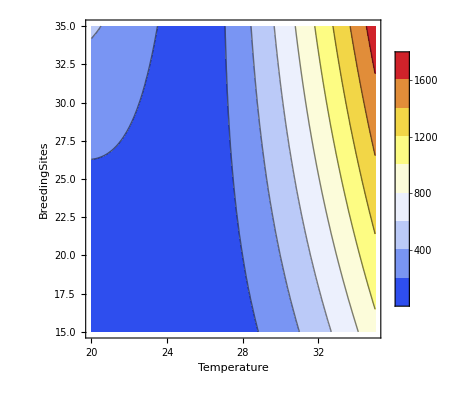
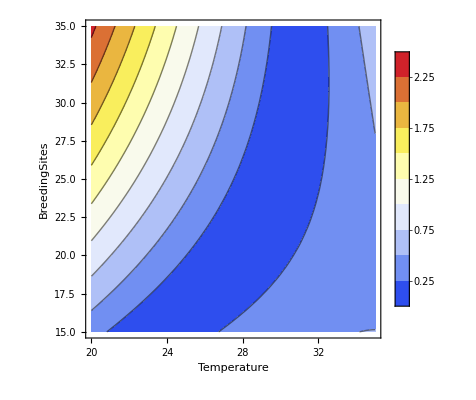
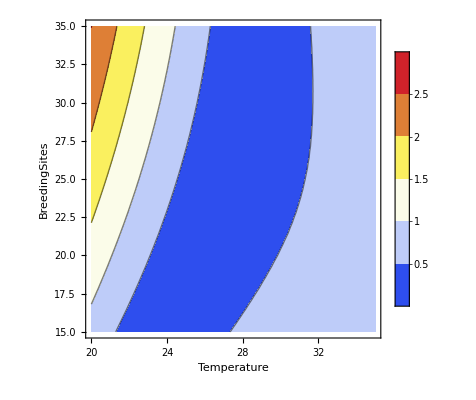

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{Plots/Fits/FitcontourDifferences.png,Plots/Fits/FitcontourRatios.png,Plots/Fits/FitcontourDifferencesSS.png,Plots/Fits/FitcontourRatiosSS.png}

{Plots/Fits/FitcontourDifferencesAbs.png,Plots/Fits/FitcontourRatiosAbs.png,Plots/Fits/FitcontourDifferencesSSAbs.png,Plots/Fits/FitcontourRatiosSSAbs.png}

{Plots/Fits/Fit3dcontourDifferences.png,Plots/Fits/Fit3dcontourRatios.png,Plots/Fits/Fit3dcontourDifferencesSS.png,Plots/Fits/Fit3dcontourRatiosSS.png}

{Plots/Fits/Fit3dcontourDifferencesAbs.png,Plots/Fits/Fit3dcontourRatiosAbs.png,Plots/Fits/Fit3dcontourDifferencesSSAbs.png,Plots/Fits/Fit3dcontourRatiosSSAbs.png}

```mathematica
Clear[BS,Temps];
factDiff[BreedingSites_,Temperature_]:=-5309+66.7 BreedingSites+391.1 Temperature+0.179 BreedingSites*BreedingSites-7.131 Temperature*Temperature-2.622 BreedingSites*Temperature
factDiffSS[BreedingSites_,Temperature_]:=-5187+98.9 BreedingSites+380.3 Temperature+0.158 BreedingSites*BreedingSites-6.856 Temperature*Temperature-4.157 BreedingSites*Temperature
factErr[BreedingSites_,Temperature_]:=0.117+0.2812 BreedingSites-0.1620 Temperature-0.000867 BreedingSites*BreedingSites+0.003825 Temperature*Temperature-0.006966 BreedingSites*Temperature
factErrSS[BreedingSites_,Temperature_]:=6.917+0.2550 BreedingSites-0.6153 Temperature-0.000863 BreedingSites*BreedingSites+0.011221 Temperature*Temperature-0.006373 BreedingSites*Temperature
funArr={factDiff[BS,Temps],factDiffSS[BS,Temps],factErr[BS,Temps],factErrSS[BS,Temps]};
c=ContourPlot[#,{Temps,20,35},{BS,15,35},FrameLabel->{"Temperature","BreedingSites"},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr
p=Plot3D[#,{Temps,20,35},{BS,15,35},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr

cAbs=ContourPlot[#//Abs,{Temps,20,35},{BS,15,35},FrameLabel->{"Temperature","BreedingSites"},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr
pAbs=Plot3D[#//Abs,{Temps,20,35},{BS,15,35},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr


Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"FitcontourDifferences.png","FitcontourRatios.png","FitcontourDifferencesSS.png","FitcontourRatiosSS.png"},c}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"FitcontourDifferencesAbs.png","FitcontourRatiosAbs.png","FitcontourDifferencesSSAbs.png","FitcontourRatiosSSAbs.png"},cAbs}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"Fit3dcontourDifferences.png","Fit3dcontourRatios.png","Fit3dcontourDifferencesSS.png","Fit3dcontourRatiosSS.png"},p}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"Fit3dcontourDifferencesAbs.png","Fit3dcontourRatiosAbs.png","Fit3dcontourDifferencesSSAbs.png","Fit3dcontourRatiosSSAbs.png"},pAbs}//Transpose)
```

```mathematica
Minimize[{Abs[#],15≤BS≤35,20≤Temps≤35},{BS,Temps}]&/@{factDiff[BS,Temps],factDiffSS[BS,Temps],factErr[BS,Temps],factErrSS[BS,Temps]}
Minimize[{Abs[factDiff[BS,Temps]+factDiffSS[BS,Temps]],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
Minimize[{Abs[factErr[BS,Temps]+factErrSS[BS,Temps]],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
Minimize[{Abs[factDiff[BS,Temps]+factDiffSS[BS,Temps]+factErr[BS,Temps]*100+factErrSS[BS,Temps]*100],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
```

{{1.81899×10^-12,{BS→30.5439,Temps→28.145}},{4.1382×10^-11,{BS→15.5287,Temps→21.2254}},{1.02141×10^-14,{BS→20.5423,Temps→27.822}},{5.76977×10^-10,{BS→31.1898,Temps→28.1857}}}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{9.09495×10^-13,{BS→15.5757,Temps→21.2838}}

{8.60556×10^-11,{BS→22.4397,Temps→27.3664}}

{2.03229×10^-10,{BS→15.0147,Temps→20.2888}}

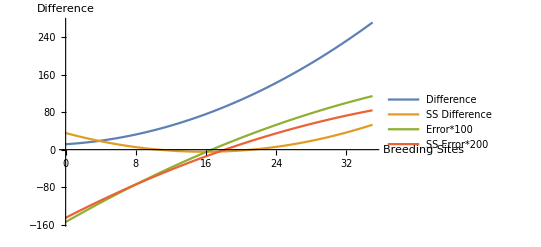

```mathematica
temp=25;
Plot[{
factDiff[bs,temp],
factDiffSS[bs,temp],
factErr[bs,temp]*100,
factErrSS[bs,temp]*100
},{bs,0,35}
,AxesLabel->{"Breeding Sites","Difference"},
PlotLegends->{"Difference","SS Difference","Error*100","SS Error*200"}]
```

## Dynamics Differences

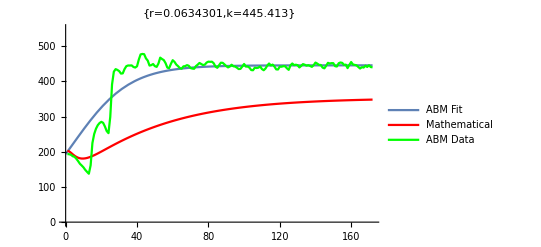

funArr

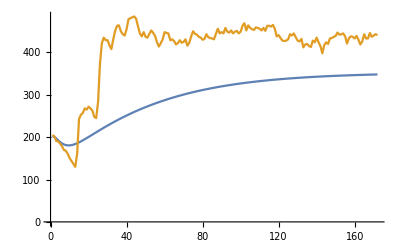

```mathematica
sampleRate=288;
point={20,25};
headTestB=HeadComparisonBetweenABMAndMathematical["/GeneratedData/ValidationSweeps/PopDynAt"<>ToString[point[[1]]]<>ToString[point[[2]]],sampleRate];
CompareABMAndMathematicalPlots[headTestB,4]
#/.{BS->point[[1]],Temps->point[[2]]}&/@funArr

ListPlot[{headTestB[[1,4]],headTestB[[2,1,4]]},Joined->True]
```

## Climate Error (see parameters export - superseeded by “Experiment 1”)

```mathematica
breedingSitesNumber=20;
timeInSection={{15,0.00039092117663288087},{16,0.0011075586658537326},{17,0.0028304175036653507},{18,0.00652445195470739},{19,0.013565960790938398},{20,0.025443269103349587},{21,0.04304409432489916},{22,0.0656862753154703},{23,0.09041860236944899},{24,0.11227015507880694},{25,0.12574626983023768},{26,0.12704296320915381},{27,0.11577928845540386},{28,0.09517776840981118},{29,0.07057708975647792},{30,0.04720786450097014},{31,0.028483000104885137},{32,0.015501576365713698},{33,0.007609959638019803},{34,0.003369786785840212},{35,0.0013459624176445084}};
errorInNumber=(factDiff[breedingSitesNumber,#[[1]]])&/@timeInSection;
errorInPercentage=(#[[2]]*factErr[breedingSitesNumber,#[[1]]])&/@timeInSection;
{errorInNumber,errorInPercentage}
```

{{-423.025,-308.256,-207.609,-121.084,-48.681,9.6,53.759,83.796,99.711,101.504,89.175,62.724,22.151,-32.544,-101.361,-184.3,-281.361,-392.544,-517.849,-657.276,-810.825},{0.000605605,0.00153008,0.00345505,0.0069601,0.0124772,0.0198356,0.0278212,0.034155,0.0362115,0.0323212,0.0229078,0.0105888,-0.000994891,-0.00891321,-0.0121263,-0.0114762,-0.00875844,-0.0056582,-0.00316295,-0.00154799,-0.0006679}}

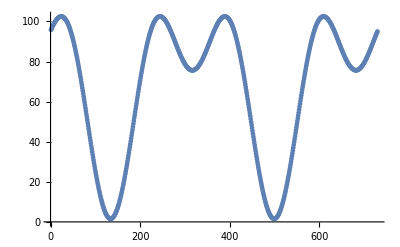
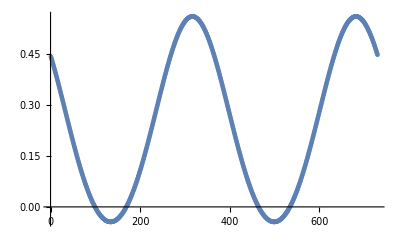

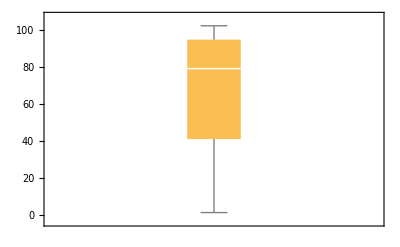
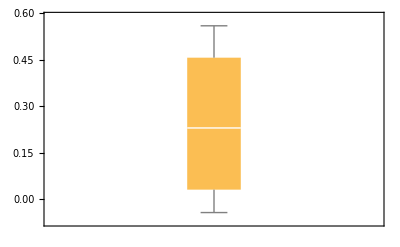

```mathematica
temps=(climateModel/.x->#)&/@Range[2*365];
{ListPlot[factDiff[breedingSitesNumber,#]&/@temps],ListPlot[factErr[breedingSitesNumber,#]&/@temps]}
{BoxWhiskerChart[factDiff[breedingSitesNumber,#]&/@temps],BoxWhiskerChart[factErr[breedingSitesNumber,#]&/@temps]}
```

## Experiment 2 : Varying Temperature

## Load Data

```mathematica
sampleRate=72;
secondsPerTick=300;
path=ParentDirectory[]<>"/GeneratedData/CatemacoBaselineNew/";
stages={"AdultPopulation","Temperature","BreedingZones"};
colorsA={Blue,Red,Green,Orange,Purple,Yellow,Brown,Black};
colorsB={LightBlue,LightRed,LightGreen,LightOrange,LightPurple,LightYellow,LightBrown,Gray};
dataRaw=ReturnData[path,stages,sampleRate];
```

## Dynamics

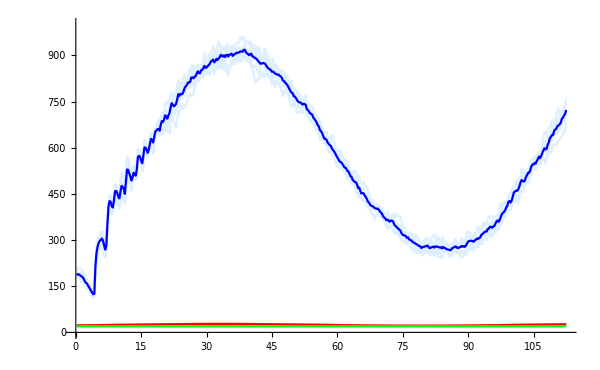
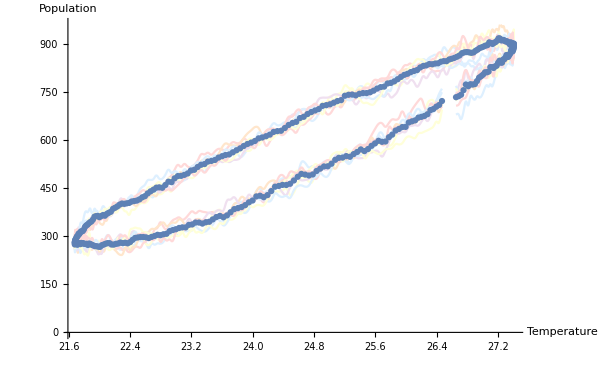
title | PopulationDynamics. | 
author | HMSC | 
date | {Tue 16 Jun 2015 17:40:36,Wed 17 Jun 2015 09:25:18} | 
description | Calibration attempts with stochastic model as reference. | 
parameter | SecondsPerTick | 300
parameter | ScenarioNumber | 2
independent | Temperature | {25}
-Graphics- | -Graphics- | AdultPopulation
-Graphics- | Temperature
-Graphics- | BreedingZones | -Graphics-
-Graphics-
-Graphics- | -Graphics-

Plots/Dynamics/header.png

Plots/Dynamics/repetitions.png

Plots/Dynamics/ellipse.png

```mathematica
{adultIndex,tempIndex}={1,2};
header=Grid[Flatten[dataRaw[[1]],1],Background->LightBlue];
repetitions=PlotRepetitions[dataRaw[[3]],stages,colorsA,colorsB,PlotRange->{0,1000}];
tempPlot=Show[TempPopPlot[dataRaw,{Thickness[.005],PointSize[.0075]},{LightBlue,LightYellow,LightRed,LightOrange,LightPurple},adultIndex,tempIndex],ImageSize->600];
Grid[{{header},{Grid[{{repetitions,tempPlot}}]}}]

Export["Plots/Dynamics/header.png",header,ImageSize->2000,ImageResolution->200]
Export["Plots/Dynamics/repetitions.png",repetitions,ImageSize->1500,ImageResolution->200]
Export["Plots/Dynamics/ellipse.png",tempPlot,ImageSize->2000,ImageResolution->200]
```

## Temp Population correlation

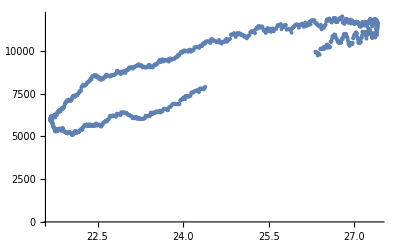
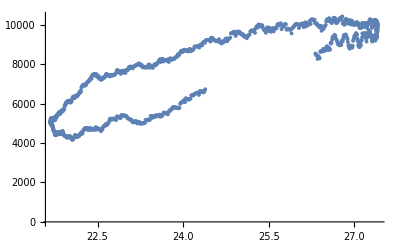
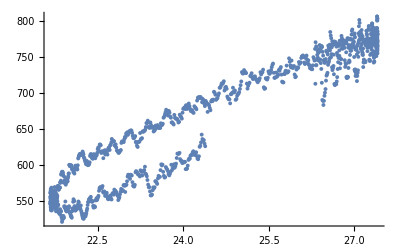
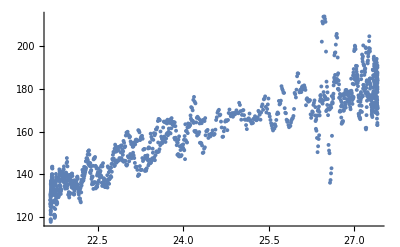
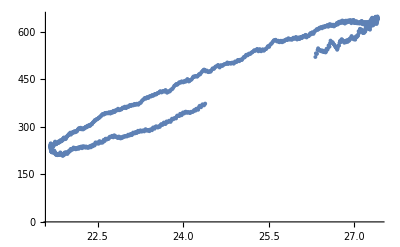
MosquitoPopulation | EggsPopulation | LarvaPopulation | PupaPopulation | AdultPopulation
0.902053 | 0.888989 | 0.95849 | 0.912921 | 0.975777
7.68471171230133×10^-509 | 1.15334204316888×10^-462 | 6.76229482070948×10^-790 | 1.41812402367543×10^-724 | 6.46685378734017×10^-1061
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Plots/Correlation/correlation.png

```mathematica
data=Table[
lowLimit=Floor[(dataRaw[[2,2,tempIndex]]//Length)*.2];
temps=dataRaw[[3,2,tempIndex]][[All,2]][[lowLimit;;All]];
popSize=dataRaw[[3,2,i]][[All,2]][[lowLimit;;All]]//N;
{Correlation[temps,popSize],CorrelationTest[{temps,popSize}//Transpose,VerifyTestAssumptions->All],ListPlot [{temps,popSize}//Transpose]}
,{i,1,5}];
correlation=Grid[Prepend[(data//Transpose),stages[[1;;5]]],Background->{None,{LightBlue}},Frame->All]

Export["Plots/Correlation/correlation.png",correlation,ImageSize->1000,ImageResolution->150]
```

## Ellipse

27761.7

6177.92 x^2-151.951 x y-239489. x+y^2+2892.16 y+2.32814×10^6==0

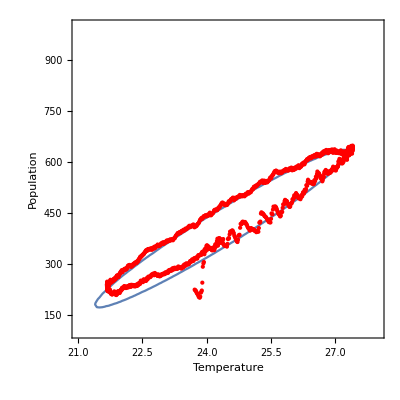

Plots/Ellipse/EllipseExperiment.png

```mathematica
Clear[l,a,b,c,d]
(*GenerateDataPoints*)
{adults,temp}={dataRaw[[2,2,5]][[100;;All]]//N,dataRaw[[2,2,tempIndex]][[100;;All]]//N};
points={temp,adults}//Transpose;
(*ModelFit*)
lin={#1^2,#1,#2,2 #1 #2,#2^2}&@@@points;
lm=LinearModelFit[lin,{1,a,b,c,d},{a,b,c,d}];
lm["AIC"]
pa=lm["BestFitParameters"];
w[x_,y_]:=pa.{1,x^2,x,y,2 x y}-y^2;
TraditionalForm[-w[x,y]==0]
ellipse=ContourPlot[w[x,y]==0,{x,21,28},{y,100,1000},Epilog->{Red,Point[points]},FrameLabel->{"Temperature","Population"}]
Export["Plots/Ellipse/EllipseExperiment.png",ellipse,ImageSize->1000,ImageResolution->150]
```

## Error Plots (first run minitab fits on Experiment 1)

### List and Whisker

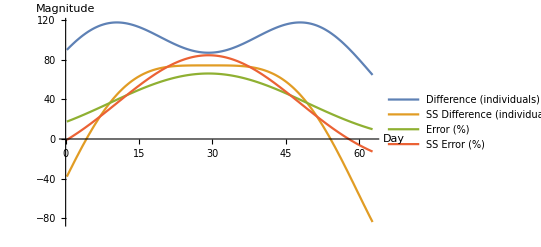

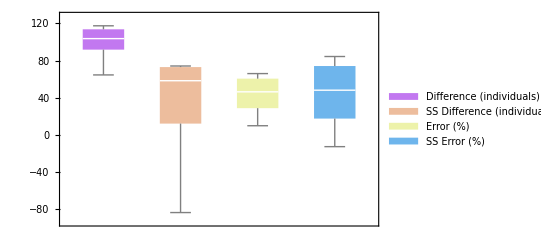

```mathematica
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,1]][[200;;All]],dataRaw[[2,2,tempIndex]][[200;;All]]};
breedingSites=ConstantArray[20,(adults//Length)]//Flatten;
(**)
plotPairs={temps,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
(**)
error1=factDiff[#[[1]],#[[2]]]&/@errorPairs;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
error3=factErr[#[[1]],#[[2]]]&/@errorPairs;
error4=factErrSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
results=Grid[{
{ListPlot[#,Joined->True,AxesLabel->{"TimeStep","Error"},ImageSize->500],BoxWhiskerChart[#,ImageSize->500]}
}]&/@{error1,error2,error3,error4};
(**)
Export["Plots/Error/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"errorDifferences.png","errorRatios.png","errorDifferencesSS.png","errorRatiosSS.png"},results}//Transpose);
ls=ListPlot[({TickToDay[#,secondsPerTick]&/@(Range[error1//Length]*sampleRate)//N,#}//Transpose)&/@{error1,error2,error3*100,error4*100},Joined->True,PlotLegends->{"Difference (individuals)","SS Difference (individuals)","Error (%)","SS Error (%)"},AxesLabel->{"Day","Magnitude"}]
bw=BoxWhiskerChart[{error1,error2,error3*100,error4*100},ChartStyle->"Pastel",ChartLegends->{"Difference (individuals)","SS Difference (individuals)","Error (%)","SS Error (%)"}]
Export["Plots/TemperatureErrors/listError.png",ls,ImageSize->1000,ImageResolution->150];
Export["Plots/TemperatureErrors/boxError.png",bw,ImageSize->1000,ImageResolution->150];
```

### Ellipse

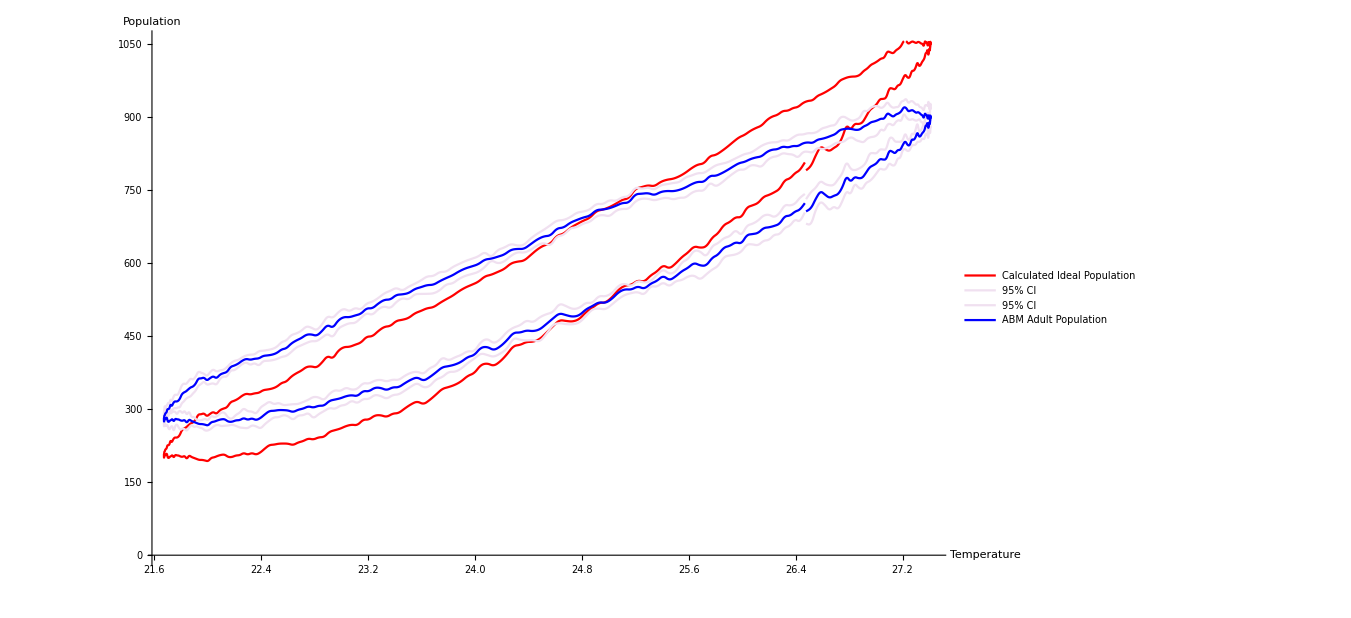

Plots/Error/errorEllipse.png

```mathematica
start=85;
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,adultIndex]][[start;;All]],dataRaw[[2,2,tempIndex]][[start;;All]]};
breedingSites=dataRaw[[2,2,3]][[start;;All]];
(**)
plotPairs={temps,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
adultsCI=MeanCI/@dataRaw[[2,1,adultIndex]][[start;;All]];
(**)
plotPairsMin={temps,adultsCI[[All,1]]}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMax={temps,adultsCI[[All,2]]}//Transpose;
(**)
plotPairsErr={temps,adults-error2}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMin={temps,adultsCI[[All,1]]}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMax={temps,adultsCI[[All,2]]}//Transpose;
(**)
errorEllipse=ListPlot[{plotPairsErr,plotPairsMin,plotPairsMax,plotPairsMean}
,Joined->True
,PlotStyle->{Red,LightPurple,LightPurple,Blue}
,PlotRange->{0,All}
,AxesLabel->{"Temperature","Population"}
,PlotLegends->{"Calculated Ideal Population","95% CI","95% CI","ABM Adult Population"}
,ImageSize->1000
,InterpolationOrder->2
]
Export["Plots/Error/errorEllipse.png",errorEllipse,ImageSize->2000,ImageResolution->300]
```

### Dynamic

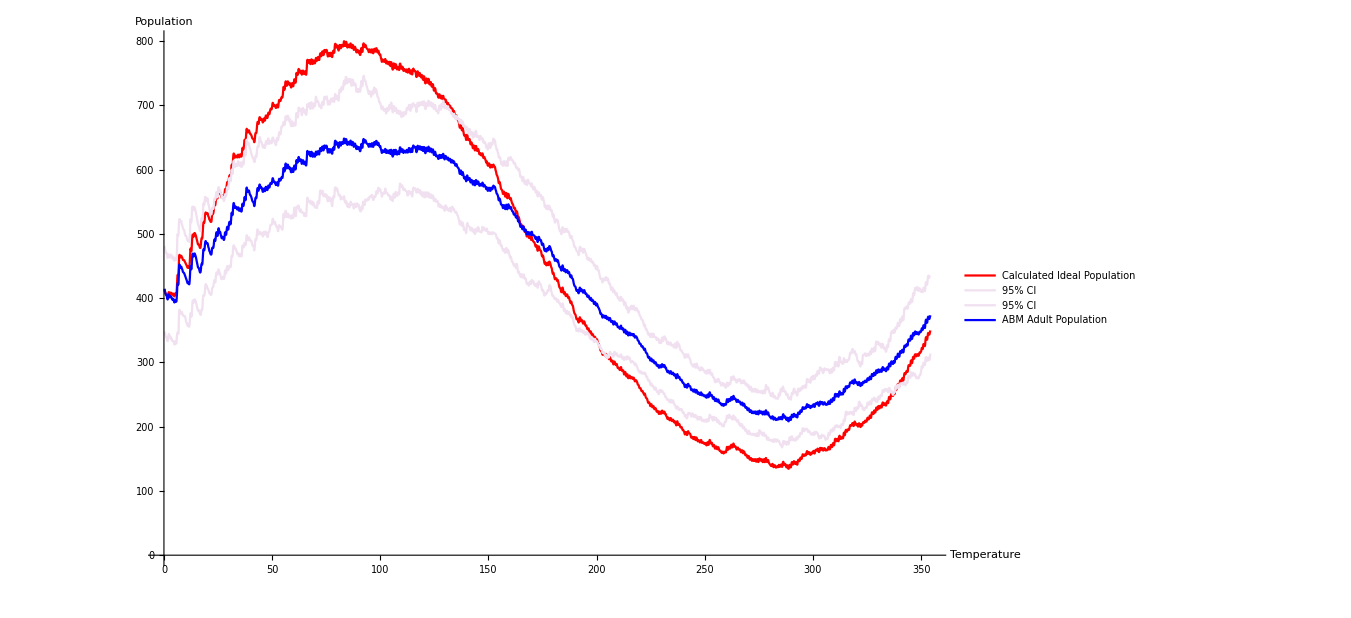

Plots/Error/errorList.png

```mathematica
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,adultIndex]][[200;;All]],dataRaw[[2,2,tempIndex]][[200;;All]]};
days=(TickToDay[#,secondsPerTick]&/@(Range[error1//Length]*sampleRate)//N);
breedingSites=ConstantArray[20,(adults//Length)]//Flatten;
(**)
plotPairs={days,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
adultsCI=MeanCI/@dataRaw[[2,1,adultIndex]][[200;;All]];
(**)
plotPairsMin={days,adultsCI[[All,1]]}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMax={days,adultsCI[[All,2]]}//Transpose;
(**)
plotPairsErr={days,adults-error2}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMin={days,adultsCI[[All,1]]}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMax={days,adultsCI[[All,2]]}//Transpose;
(**)
errorEllipse=ListPlot[{plotPairsErr,plotPairsMin,plotPairsMax,plotPairsMean}
,Joined->True
,PlotStyle->{Red,LightPurple,LightPurple,Blue}
,PlotRange->{0,All}
,AxesLabel->{"Temperature","Population"}
,PlotLegends->{"Calculated Ideal Population","95% CI","95% CI","ABM Adult Population"}
,ImageSize->1000
,InterpolationOrder->2
]
Export["Plots/Error/errorList.png",errorEllipse,ImageSize->2000,ImageResolution->300]
```

## Experiment 3 : Optimisation

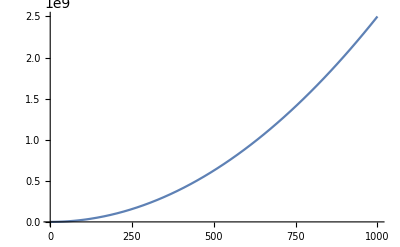

```mathematica
costPerIndividual=50;
(*MinimisationFitnessFunction*)
FitnesFunction[population_,costPerIndividual_,releasesNumber_]:=population+(costPerIndividual*releasesNumber)^2
Plot[FitnesFunction[500,costPerIndividual,releasedIndividuals],{releasedIndividuals,1,1000}]
```

## Experiment 4 : Network

## Network

```mathematica
mixFunction=Mean;
imageSize=500;
edgeshape[e_,___]:={Arrowheads[{{.0005,.5}}],Arrow[e]};
varStyle="Both";
graphLay="CircularEmbedding";
vSize=.5;
lThick=.0025;
clusteringMethod="Modularity";
mixFunction=Median;
```

### Direct

```mathematica
SetDirectory[NotebookDirectory[]];
path=ParentDirectory[]<>"/GeneratedData/PopDynAt20";
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetExperimentDescription*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
(*GetContactsSection*)
cSect=GetExperimentsSetContactsSection[xmlSet];
(*GetTransitionsMatrix*)
labels=GetExperimentsSetContactLabels[cSect];
contactsMatrix=GetExperimentSetContactsTransitionsWithPattern[cSect,labels,mixFunction];
contactsMatrices=GetExperimentSetRawContactsTransitionsWithPattern[cSect,labels];
(*GraphTransitions*)
frequenciesGraph=GraphTransitionsFrequencies[contactsMatrix,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
frequenciesScale=GridColorScaleFrequency[10,10,contactsMatrix];
(*Communities*)
communities=FindGraphCommunities[frequenciesGraph,Method->clusteringMethod];
communitiesGraph=CommunityGraphPlot[frequenciesGraph,communities,ImageSize->imageSize]
```

-Graphics-

### Bites

```mathematica
SetDirectory[NotebookDirectory[]];
path=ParentDirectory[]<>"/GeneratedData/PopDynAt20";
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bites=GetExperimentsSetBitesSection[xmlSet];
labels=GetExperimentsSetBiteLabels[bites];
bitesMatrix=GetExperimentsSetBitesTransitionsWithPattern[bites,labels,mixFunction];
bitesMatrices=GetExperimentsSetRawBitesTransitionsWithPattern[bites,labels];
frequenciesGraph=GraphTransitionsFrequencies[bitesMatrix,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
frequenciesScale=GridColorScaleFrequency[10,10,bitesMatrix];
communities=FindGraphCommunities[frequenciesGraph,Method->clusteringMethod];
communitiesGraph=CommunityGraphPlot[frequenciesGraph,communities,ImageSize->imageSize]
```

-Graphics-